```mathematica
p=Integrate[(y-x)(1/(Exp[y-x]-1)+1/(Exp[-x]+1))(1/(Exp[w+x]+1)+1/(Exp[w-x]+1)), {x,y-J,y+J}, 
Assumptions->w>0&&J>0&&y>0&&β>0];
f=1/J FullSimplify[p, Assumptions->y>0&&J>0]/.{J-> β*J,y-> β*ω}
g=f/.{J->1}
```

1/((-1+ⅇ^w) (ⅇ^w+ⅇ^(β ω)) (1+ⅇ^(w+β ω)) J β)(1/6 (ⅇ^w (-2 (-1+ⅇ^w) π^2+6 J (2 ⅈ (-1+ⅇ^w) π+w) β+3 (-3+ⅇ^w) J^2 β^2)+ⅇ^(w+2 β ω) (-2 (-1+ⅇ^w) π^2+6 J (2 ⅈ (-1+ⅇ^w) π+ⅇ^w w) β-3 (1+ⅇ^w) J^2 β^2)+2 ⅇ^(β ω) (-2 (-1+ⅇ^w) π^2+3 J (4 ⅈ (-1+ⅇ^w) π+ⅇ^w (1+ⅇ^w) w) β-3 (1+ⅇ^(2 w)) J^2 β^2)+12 (-1+ⅇ^w) (ⅇ^w+2 ⅇ^(β ω)+ⅇ^(w+2 β ω)) J β Log[-1+ⅇ^(J β)]+24 ⅇ^(w+β ω) J β (Cosh[w]+Cosh[β ω]) Log[(ⅇ^(J β)+ⅇ^(β ω)) (1+ⅇ^(J β+β ω))]-6 ⅇ^w (1+ⅇ^(β ω)) J β ((1+ⅇ^(w+β ω)) Log[1+ⅇ^(-w-J β+β ω)]+(1+ⅇ^(w+β ω)) Log[ⅇ^w+ⅇ^(J β+β ω)]+(ⅇ^w+ⅇ^(β ω)) (Log[ⅇ^(J β)+ⅇ^(w+β ω)]+Log[1+ⅇ^(w+J β+β ω)])))+2 (-1+ⅇ^w) (ⅇ^w+2 ⅇ^(β ω)+ⅇ^(w+2 β ω)) PolyLog[2,ⅇ^(J β)]-2 (ⅇ^w+ⅇ^(β ω)) (1+ⅇ^(w+β ω)) PolyLog[2,-ⅇ^(-J β+β ω)]+ⅇ^w (1+ⅇ^(β ω)) (1+ⅇ^(w+β ω)) PolyLog[2,-ⅇ^(-w-J β+β ω)]+ⅇ^w (1+ⅇ^(β ω)) (ⅇ^w+ⅇ^(β ω)) PolyLog[2,-ⅇ^(w-J β+β ω)]+2 (ⅇ^w+ⅇ^(β ω)) (1+ⅇ^(w+β ω)) PolyLog[2,-ⅇ^(J β+β ω)]-ⅇ^w (1+ⅇ^(β ω)) (1+ⅇ^(w+β ω)) PolyLog[2,-ⅇ^(-w+J β+β ω)]-ⅇ^w (1+ⅇ^(β ω)) (ⅇ^w+ⅇ^(β ω)) PolyLog[2,-ⅇ^(w+J β+β ω)])

1/((-1+ⅇ^w) (ⅇ^w+ⅇ^(β ω)) (1+ⅇ^(w+β ω)) β)(1/6 (ⅇ^w (-2 (-1+ⅇ^w) π^2+6 (2 ⅈ (-1+ⅇ^w) π+w) β+3 (-3+ⅇ^w) β^2)+ⅇ^(w+2 β ω) (-2 (-1+ⅇ^w) π^2+6 (2 ⅈ (-1+ⅇ^w) π+ⅇ^w w) β-3 (1+ⅇ^w) β^2)+2 ⅇ^(β ω) (-2 (-1+ⅇ^w) π^2+3 (4 ⅈ (-1+ⅇ^w) π+ⅇ^w (1+ⅇ^w) w) β-3 (1+ⅇ^(2 w)) β^2)+12 (-1+ⅇ^w) (ⅇ^w+2 ⅇ^(β ω)+ⅇ^(w+2 β ω)) β Log[-1+ⅇ^β]+24 ⅇ^(w+β ω) β (Cosh[w]+Cosh[β ω]) Log[(ⅇ^β+ⅇ^(β ω)) (1+ⅇ^(β+β ω))]-6 ⅇ^w (1+ⅇ^(β ω)) β ((1+ⅇ^(w+β ω)) Log[1+ⅇ^(-w-β+β ω)]+(1+ⅇ^(w+β ω)) Log[ⅇ^w+ⅇ^(β+β ω)]+(ⅇ^w+ⅇ^(β ω)) (Log[ⅇ^β+ⅇ^(w+β ω)]+Log[1+ⅇ^(w+β+β ω)])))+2 (-1+ⅇ^w) (ⅇ^w+2 ⅇ^(β ω)+ⅇ^(w+2 β ω)) PolyLog[2,ⅇ^β]-2 (ⅇ^w+ⅇ^(β ω)) (1+ⅇ^(w+β ω)) PolyLog[2,-ⅇ^(-β+β ω)]+ⅇ^w (1+ⅇ^(β ω)) (1+ⅇ^(w+β ω)) PolyLog[2,-ⅇ^(-w-β+β ω)]+ⅇ^w (1+ⅇ^(β ω)) (ⅇ^w+ⅇ^(β ω)) PolyLog[2,-ⅇ^(w-β+β ω)]+2 (ⅇ^w+ⅇ^(β ω)) (1+ⅇ^(w+β ω)) PolyLog[2,-ⅇ^(β+β ω)]-ⅇ^w (1+ⅇ^(β ω)) (1+ⅇ^(w+β ω)) PolyLog[2,-ⅇ^(-w+β+β ω)]-ⅇ^w (1+ⅇ^(β ω)) (ⅇ^w+ⅇ^(β ω)) PolyLog[2,-ⅇ^(w+β+β ω)])

```mathematica
(1/((-1+ⅇ^w) (ⅇ^w+ⅇ^(β ω)) (1+ⅇ^(w+β ω)) J β)(1/6 (ⅇ^w (-2 (-1+ⅇ^w) π^2+6 J (2 ⅈ (-1+ⅇ^w) π+w) β+3 (-3+ⅇ^w) J^2 β^2)+ⅇ^(w+2 β ω) (-2 (-1+ⅇ^w) π^2+6 J (2 ⅈ (-1+ⅇ^w) π+ⅇ^w w) β-3 (1+ⅇ^w) J^2 β^2)+2 ⅇ^(β ω) (-2 (-1+ⅇ^w) π^2+3 J (4 ⅈ (-1+ⅇ^w) π+ⅇ^w (1+ⅇ^w) w) β-3 (1+ⅇ^(2 w)) J^2 β^2)+12 (-1+ⅇ^w) (ⅇ^w+2 ⅇ^(β ω)+ⅇ^(w+2 β ω)) J β Log[-1+ⅇ^(J β)]+24 ⅇ^(w+β ω) J β (Cosh[w]+Cosh[β ω]) Log[(ⅇ^(J β)+ⅇ^(β ω)) (1+ⅇ^(J β+β ω))]-6 ⅇ^w (1+ⅇ^(β ω)) J β ((1+ⅇ^(w+β ω)) Log[1+ⅇ^(-w-J β+β ω)]+(1+ⅇ^(w+β ω)) Log[ⅇ^w+ⅇ^(J β+β ω)]+(ⅇ^w+ⅇ^(β ω)) (Log[ⅇ^(J β)+ⅇ^(w+β ω)]+Log[1+ⅇ^(w+J β+β ω)])))+2 (-1+ⅇ^w) (ⅇ^w+2 ⅇ^(β ω)+ⅇ^(w+2 β ω)) PolyLog[2,ⅇ^(J β)]-2 (ⅇ^w+ⅇ^(β ω)) (1+ⅇ^(w+β ω)) PolyLog[2,-ⅇ^(-J β+β ω)]+ⅇ^w (1+ⅇ^(β ω)) (1+ⅇ^(w+β ω)) PolyLog[2,-ⅇ^(-w-J β+β ω)]+ⅇ^w (1+ⅇ^(β ω)) (ⅇ^w+ⅇ^(β ω)) PolyLog[2,-ⅇ^(w-J β+β ω)]+2 (ⅇ^w+ⅇ^(β ω)) (1+ⅇ^(w+β ω)) PolyLog[2,-ⅇ^(J β+β ω)]-ⅇ^w (1+ⅇ^(β ω)) (1+ⅇ^(w+β ω)) PolyLog[2,-ⅇ^(-w+J β+β ω)]-ⅇ^w (1+ⅇ^(β ω)) (ⅇ^w+ⅇ^(β ω)) PolyLog[2,-ⅇ^(w+J β+β ω)]))/.w->β ω0
```

1/((-1+ⅇ^(β ω0)) (ⅇ^(β ω)+ⅇ^(β ω0)) (1+ⅇ^(β ω+β ω0)) J β)(1/6 (ⅇ^(β ω0) (-2 (-1+ⅇ^(β ω0)) π^2+3 (-3+ⅇ^(β ω0)) J^2 β^2+6 J β (2 ⅈ (-1+ⅇ^(β ω0)) π+β ω0))+ⅇ^(2 β ω+β ω0) (-2 (-1+ⅇ^(β ω0)) π^2-3 (1+ⅇ^(β ω0)) J^2 β^2+6 J β (2 ⅈ (-1+ⅇ^(β ω0)) π+ⅇ^(β ω0) β ω0))+2 ⅇ^(β ω) (-2 (-1+ⅇ^(β ω0)) π^2-3 (1+ⅇ^(2 β ω0)) J^2 β^2+3 J β (4 ⅈ (-1+ⅇ^(β ω0)) π+ⅇ^(β ω0) (1+ⅇ^(β ω0)) β ω0))+12 (-1+ⅇ^(β ω0)) (2 ⅇ^(β ω)+ⅇ^(β ω0)+ⅇ^(2 β ω+β ω0)) J β Log[-1+ⅇ^(J β)]+24 ⅇ^(β ω+β ω0) J β (Cosh[β ω]+Cosh[β ω0]) Log[(ⅇ^(J β)+ⅇ^(β ω)) (1+ⅇ^(J β+β ω))]-6 ⅇ^(β ω0) (1+ⅇ^(β ω)) J β ((1+ⅇ^(β ω+β ω0)) Log[ⅇ^(J β+β ω)+ⅇ^(β ω0)]+(1+ⅇ^(β ω+β ω0)) Log[1+ⅇ^(-J β+β ω-β ω0)]+(ⅇ^(β ω)+ⅇ^(β ω0)) (Log[ⅇ^(J β)+ⅇ^(β ω+β ω0)]+Log[1+ⅇ^(J β+β ω+β ω0)])))+2 (-1+ⅇ^(β ω0)) (2 ⅇ^(β ω)+ⅇ^(β ω0)+ⅇ^(2 β ω+β ω0)) PolyLog[2,ⅇ^(J β)]-2 (ⅇ^(β ω)+ⅇ^(β ω0)) (1+ⅇ^(β ω+β ω0)) PolyLog[2,-ⅇ^(-J β+β ω)]+2 (ⅇ^(β ω)+ⅇ^(β ω0)) (1+ⅇ^(β ω+β ω0)) PolyLog[2,-ⅇ^(J β+β ω)]+ⅇ^(β ω0) (1+ⅇ^(β ω)) (1+ⅇ^(β ω+β ω0)) PolyLog[2,-ⅇ^(-J β+β ω-β ω0)]-ⅇ^(β ω0) (1+ⅇ^(β ω)) (1+ⅇ^(β ω+β ω0)) PolyLog[2,-ⅇ^(J β+β ω-β ω0)]+ⅇ^(β ω0) (1+ⅇ^(β ω)) (ⅇ^(β ω)+ⅇ^(β ω0)) PolyLog[2,-ⅇ^(-J β+β ω+β ω0)]-ⅇ^(β ω0) (1+ⅇ^(β ω)) (ⅇ^(β ω)+ⅇ^(β ω0)) PolyLog[2,-ⅇ^(J β+β ω+β ω0)])

```mathematica
FullSimplify[1/((-1+ⅇ^(β ω0)) (ⅇ^(β ω)+ⅇ^(β ω0)) (1+ⅇ^(β ω+β ω0)) J β)(1/6 (ⅇ^(β ω0) (-2 (-1+ⅇ^(β ω0)) π^2+3 (-3+ⅇ^(β ω0)) J^2 β^2+6 J β (2 ⅈ (-1+ⅇ^(β ω0)) π+β ω0))+ⅇ^(2 β ω+β ω0) (-2 (-1+ⅇ^(β ω0)) π^2-3 (1+ⅇ^(β ω0)) J^2 β^2+6 J β (2 ⅈ (-1+ⅇ^(β ω0)) π+ⅇ^(β ω0) β ω0))+2 ⅇ^(β ω) (-2 (-1+ⅇ^(β ω0)) π^2-3 (1+ⅇ^(2 β ω0)) J^2 β^2+3 J β (4 ⅈ (-1+ⅇ^(β ω0)) π+ⅇ^(β ω0) (1+ⅇ^(β ω0)) β ω0))+12 (-1+ⅇ^(β ω0)) (2 ⅇ^(β ω)+ⅇ^(β ω0)+ⅇ^(2 β ω+β ω0)) J β Log[-1+ⅇ^(J β)]+24 ⅇ^(β ω+β ω0) J β (Cosh[β ω]+Cosh[β ω0]) Log[(ⅇ^(J β)+ⅇ^(β ω)) (1+ⅇ^(J β+β ω))]-6 ⅇ^(β ω0) (1+ⅇ^(β ω)) J β ((1+ⅇ^(β ω+β ω0)) Log[ⅇ^(J β+β ω)+ⅇ^(β ω0)]+(1+ⅇ^(β ω+β ω0)) Log[1+ⅇ^(-J β+β ω-β ω0)]+(ⅇ^(β ω)+ⅇ^(β ω0)) (Log[ⅇ^(J β)+ⅇ^(β ω+β ω0)]+Log[1+ⅇ^(J β+β ω+β ω0)])))+2 (-1+ⅇ^(β ω0)) (2 ⅇ^(β ω)+ⅇ^(β ω0)+ⅇ^(2 β ω+β ω0)) PolyLog[2,ⅇ^(J β)]-2 (ⅇ^(β ω)+ⅇ^(β ω0)) (1+ⅇ^(β ω+β ω0)) PolyLog[2,-ⅇ^(-J β+β ω)]+2 (ⅇ^(β ω)+ⅇ^(β ω0)) (1+ⅇ^(β ω+β ω0)) PolyLog[2,-ⅇ^(J β+β ω)]+ⅇ^(β ω0) (1+ⅇ^(β ω)) (1+ⅇ^(β ω+β ω0)) PolyLog[2,-ⅇ^(-J β+β ω-β ω0)]-ⅇ^(β ω0) (1+ⅇ^(β ω)) (1+ⅇ^(β ω+β ω0)) PolyLog[2,-ⅇ^(J β+β ω-β ω0)]+ⅇ^(β ω0) (1+ⅇ^(β ω)) (ⅇ^(β ω)+ⅇ^(β ω0)) PolyLog[2,-ⅇ^(-J β+β ω+β ω0)]-ⅇ^(β ω0) (1+ⅇ^(β ω)) (ⅇ^(β ω)+ⅇ^(β ω0)) PolyLog[2,-ⅇ^(J β+β ω+β ω0)]), Assumptions->β>0&&ω>0&&J>0&&ω0>0]
```

1/((-1+ⅇ^(β ω0)) (ⅇ^(β ω)+ⅇ^(β ω0)) (1+ⅇ^(β (ω+ω0))) J β)(1/6 (ⅇ^(β (2 ω+ω0)) (-2 (-1+ⅇ^(β ω0)) π^2+12 ⅈ (-1+ⅇ^(β ω0)) J π β-3 J β^2 (J+ⅇ^(β ω0) (J-2 ω0)))+ⅇ^(β ω0) (-2 (-1+ⅇ^(β ω0)) π^2+12 ⅈ (-1+ⅇ^(β ω0)) J π β+3 J β^2 ((-3+ⅇ^(β ω0)) J+2 ω0))+2 ⅇ^(β ω) (-2 (-1+ⅇ^(β ω0)) π^2+12 ⅈ (-1+ⅇ^(β ω0)) J π β-3 J β^2 (J+ⅇ^(2 β ω0) (J-ω0)-ⅇ^(β ω0) ω0))+12 (-1+ⅇ^(β ω0)) (2 ⅇ^(β ω)+ⅇ^(β ω0)+ⅇ^(β (2 ω+ω0))) J β Log[-1+ⅇ^(J β)]+24 ⅇ^(β (ω+ω0)) J β (Cosh[β ω]+Cosh[β ω0]) Log[(ⅇ^(J β)+ⅇ^(β ω)) (1+ⅇ^(β (J+ω)))]-6 ⅇ^(β ω0) (1+ⅇ^(β ω)) J β ((1+ⅇ^(β (ω+ω0))) Log[(ⅇ^(β (J+ω))+ⅇ^(β ω0)) (1+ⅇ^(-β (J-ω+ω0)))]+(ⅇ^(β ω)+ⅇ^(β ω0)) Log[(ⅇ^(J β)+ⅇ^(β (ω+ω0))) (1+ⅇ^(β (J+ω+ω0)))]))+2 (-1+ⅇ^(β ω0)) (2 ⅇ^(β ω)+ⅇ^(β ω0)+ⅇ^(β (2 ω+ω0))) PolyLog[2,ⅇ^(J β)]-2 (ⅇ^(β ω)+ⅇ^(β ω0)) (1+ⅇ^(β (ω+ω0))) PolyLog[2,-ⅇ^(β (-J+ω))]+2 (ⅇ^(β ω)+ⅇ^(β ω0)) (1+ⅇ^(β (ω+ω0))) PolyLog[2,-ⅇ^(β (J+ω))]-ⅇ^(β ω0) (1+ⅇ^(β ω)) (1+ⅇ^(β (ω+ω0))) PolyLog[2,-ⅇ^(β (J+ω-ω0))]+ⅇ^(β ω0) (1+ⅇ^(β ω)) (1+ⅇ^(β (ω+ω0))) PolyLog[2,-ⅇ^(-β (J-ω+ω0))]+ⅇ^(β ω0) (1+ⅇ^(β ω)) (ⅇ^(β ω)+ⅇ^(β ω0)) PolyLog[2,-ⅇ^(β (-J+ω+ω0))]-ⅇ^(β ω0) (1+ⅇ^(β ω)) (ⅇ^(β ω)+ⅇ^(β ω0)) PolyLog[2,-ⅇ^(β (J+ω+ω0))])

# Another expression for Y(nu, omega)

```mathematica
p=Integrate[x/J(1/(Exp[x]-1)+1/(Exp[x- ω]+1)), {x,-J,+J}, 
Assumptions->ω>0&&J>0&&y>0];
f=FullSimplify[p, Assumptions->ω>0&&J>0]
```

(-J (J-ⅈ π+ω+Log[2]-2 Log[-1+ⅇ^J]+Log[Cosh[J]+Cosh[ω]])-PolyLog[2,ⅇ^-J]+PolyLog[2,ⅇ^J]+PolyLog[2,-ⅇ^(-J+ω)]-PolyLog[2,-ⅇ^(J+ω)])/J

```mathematica
p=Integrate[x/J(1/(Exp[x]-1)+1/(Exp[x]+1)), {x,-J,+J}, 
Assumptions->J>0];
f=FullSimplify[p, Assumptions->J>0]
```

-(-4 ⅈ J π+π^2+8 J ArcCoth[ⅇ^J]+4 PolyLog[2,-ⅇ^J]-4 PolyLog[2,ⅇ^J])/(2 J)

## test for simplification

```mathematica
FullSimplify[(-J (J-ⅈ π+ω+Log[2]-2 Log[-1+ⅇ^J]+Log[Cosh[J]+Cosh[ω]])-PolyLog[2,ⅇ^-J]+PolyLog[2,ⅇ^J]+PolyLog[2,-ⅇ^(-J+ω)]-PolyLog[2,-ⅇ^(J+ω)])/J-(-J/2- Log[(1+ⅇ^(J-ω))(1+ⅇ^(-J-ω))]+(PolyLog[2,-ⅇ^(-J-ω)]-PolyLog[2,-ⅇ^(J-ω)]-2PolyLog[2,1-ⅇ^J])/J), Assumptions->ω>0&&J>0]
```

(-3 J^2+π^2+6 J Log[-1+ⅇ^J]-6 PolyLog[2,ⅇ^-J]+6 PolyLog[2,1-ⅇ^J])/(6 J)

```mathematica
(-J (J-ⅈ π+ω+Log[2]-2 Log[-1+ⅇ^J]+Log[Cosh[J]+Cosh[ω]])-PolyLog[2,ⅇ^-J]+PolyLog[2,ⅇ^J]+PolyLog[2,-ⅇ^(-J+ω)]-PolyLog[2,-ⅇ^(J+ω)])/J/.ω->0
```

```mathematica
(-J (J-ⅈ π+Log[2]-2 Log[-1+ⅇ^J]+Log[1+Cosh[J]])+PolyLog[2,-ⅇ^-J]-PolyLog[2,ⅇ^-J]-PolyLog[2,-ⅇ^J]+PolyLog[2,ⅇ^J])/J/.J->0.00001
```

2.+3.0479×10^-11 ⅈ

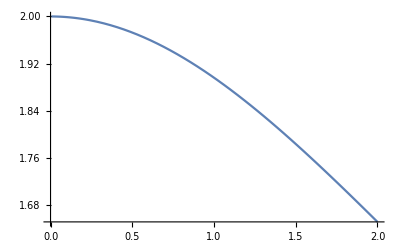

```mathematica
Plot[(-J (J-ⅈ π+Log[2]-2 Log[-1+ⅇ^J]+Log[1+Cosh[J]])+PolyLog[2,-ⅇ^-J]-PolyLog[2,ⅇ^-J]-PolyLog[2,-ⅇ^J]+PolyLog[2,ⅇ^J])/J,{J,0,2}]
```

```mathematica
(-J (J-ⅈ π+ω+Log[2]-2 Log[-1+ⅇ^J]+Log[Cosh[J]+Cosh[ω]])-PolyLog[2,ⅇ^-J]+PolyLog[2,ⅇ^J]+PolyLog[2,-ⅇ^(-J+ω)]-PolyLog[2,-ⅇ^(J+ω)])/J/.{J->1/T,ω->ω/T}
```

T (-(-ⅈ π+1/T+ω/T+Log[2]-2 Log[-1+ⅇ^(1/T)]+Log[Cosh[1/T]+Cosh[ω/T]])/T-PolyLog[2,ⅇ^(-1/T)]+PolyLog[2,ⅇ^(1/T)]+PolyLog[2,-ⅇ^(-1/T+ω/T)]-PolyLog[2,-ⅇ^(1/T+ω/T)])

```mathematica
Manipulate[Plot[T (-(-ⅈ π+1/T+ω/T+Log[2]-2 Log[-1+ⅇ^(1/T)]+Log[Cosh[1/T]+Cosh[ω/T]])/T-PolyLog[2,ⅇ^(-1/T)]+PolyLog[2,ⅇ^(1/T)]+PolyLog[2,-ⅇ^(-1/T+ω/T)]-PolyLog[2,-ⅇ^(1/T+ω/T)]),{ω,0,10}],{T,1,10}]
```

```mathematica
1/T(1/2+2 y-T Log[(ⅇ^(1/T)+ⅇ^(y/T)) (1+ⅇ^((1+y)/T))]+T^2 (2 (-PolyLog[2,1-ⅇ^(1/T)])-PolyLog[2,-ⅇ^((1-y)/T)]+PolyLog[2,-ⅇ^(-(1+y)/T)]))/.y->ω
```

(1/2+2 ω-T Log[(ⅇ^(1/T)+ⅇ^(ω/T)) (1+ⅇ^((1+ω)/T))]+T^2 (-PolyLog[2,-ⅇ^((1-ω)/T)]+PolyLog[2,-ⅇ^(-(1+ω)/T)]-2 PolyLog[2,1-ⅇ^(1/T)]))/T

```mathematica
FullSimplify[T (-(-ⅈ π+1/T+ω/T+Log[2]-2 Log[-1+ⅇ^(1/T)]+Log[Cosh[1/T]+Cosh[ω/T]])/T-PolyLog[2,ⅇ^(-1/T)]+PolyLog[2,ⅇ^(1/T)]+PolyLog[2,-ⅇ^(-1/T+ω/T)]-PolyLog[2,-ⅇ^(1/T+ω/T)])-(1/2+2 ω-T Log[(ⅇ^(1/T)+ⅇ^(ω/T)) (1+ⅇ^((1+ω)/T))]+T^2 (-PolyLog[2,-ⅇ^((1-ω)/T)]+PolyLog[2,-ⅇ^(-(1+ω)/T)]-2 PolyLog[2,1-ⅇ^(1/T)]))/T,Assumptions->ω>0&&T>0]
```

(π^2 T)/3+((-2+ω) ω)/(2 T)+Log[-1+ⅇ^(1/T)]+T (-PolyLog[2,ⅇ^(-1/T)]+PolyLog[2,-ⅇ^((1-ω)/T)]+PolyLog[2,-ⅇ^((-1+ω)/T)]+PolyLog[2,1-ⅇ^(1/T)])

```mathematica
Manipulate[Plot[{T (-(-ⅈ π+1/T+ω/T+Log[2]-2 Log[-1+ⅇ^(1/T)]+Log[Cosh[1/T]+Cosh[ω/T]])/T-PolyLog[2,ⅇ^(-1/T)]+PolyLog[2,ⅇ^(1/T)]+PolyLog[2,-ⅇ^(-1/T+ω/T)]-PolyLog[2,-ⅇ^(1/T+ω/T)]),1/T(1/2+2 ω-T Log[(ⅇ^(1/T)+ⅇ^(ω/T)) (1+ⅇ^((1+ω)/T))]+T^2 (-PolyLog[2,-ⅇ^((1-ω)/T)]+PolyLog[2,-ⅇ^(-(1+ω)/T)]-2 PolyLog[2,1-ⅇ^(1/T)]))},{ω,0,10}],{T,1,10}]
```

```mathematica
(1/(J T)(-J^2/2+2 J y-J T Log[(1+ⅇ^((y-J)/T)) (1+ⅇ^((J+y)/T))]+T^2 (-2 PolyLog[2,1-ⅇ^(J/T)]-PolyLog[2,-ⅇ^((J-y)/T)]+PolyLog[2,-ⅇ^(-(J+y)/T)])))/.T->1
```

(-J^2/2+2 J y-J Log[(1+ⅇ^(-J+y)) (1+ⅇ^(J+y))]+PolyLog[2,-ⅇ^(-J-y)]-PolyLog[2,-ⅇ^(J-y)]-2 PolyLog[2,1-ⅇ^J])/J

```mathematica
(1/(J T)(-J^2/2+2 J y-J T Log[(1+ⅇ^((y-J)/T)) (1+ⅇ^((J+y)/T))]+T^2 (-2 PolyLog[2,1-ⅇ^(J/T)]-PolyLog[2,-ⅇ^((J-y)/T)]+PolyLog[2,-ⅇ^(-(J+y)/T)])))/.J->1
```

(-1/2+2 y-T Log[(1+ⅇ^((-1+y)/T)) (1+ⅇ^((1+y)/T))]+T^2 (-PolyLog[2,-ⅇ^((1-y)/T)]+PolyLog[2,-ⅇ^(-(1+y)/T)]-2 PolyLog[2,1-ⅇ^(1/T)]))/T

```mathematica
FullSimplify[1/T(1/2+2 y-T Log[(ⅇ^(1/T)+ⅇ^(y/T)) (1+ⅇ^((1+y)/T))]+T^2 (2 (-PolyLog[2,1-ⅇ^(1/T)])-PolyLog[2,-ⅇ^((1-y)/T)]+PolyLog[2,-ⅇ^(-(1+y)/T)]))-(-1/2+2 y-T Log[(1+ⅇ^((-1+y)/T)) (1+ⅇ^((1+y)/T))]+T^2 (-PolyLog[2,-ⅇ^((1-y)/T)]+PolyLog[2,-ⅇ^(-(1+y)/T)]-2 PolyLog[2,1-ⅇ^(1/T)]))/T,Assumptions->y>0&&T>0]
```

0

```mathematica
(-J^2/2+2 J y-J Log[(1+ⅇ^(-J+y)) (1+ⅇ^(J+y))]+PolyLog[2,-ⅇ^(-J-y)]-PolyLog[2,-ⅇ^(J-y)]-2 PolyLog[2,1-ⅇ^J])/J/.y->ω
```

```mathematica
FullSimplify[(-J^2/2+2 J ω-J Log[(1+ⅇ^(-J+ω)) (1+ⅇ^(J+ω))]+PolyLog[2,-ⅇ^(-J-ω)]-PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,1-ⅇ^J])/J-(-J (J-ⅈ π+ω+Log[2]-2 Log[-1+ⅇ^J]+Log[Cosh[J]+Cosh[ω]])-PolyLog[2,ⅇ^-J]+PolyLog[2,ⅇ^J]+PolyLog[2,-ⅇ^(-J+ω)]-PolyLog[2,-ⅇ^(J+ω)])/J,Assumptions->ω>0&&J>0]
```

-(-3 J^2+π^2+6 J Log[-1+ⅇ^J]-6 PolyLog[2,ⅇ^-J]+6 PolyLog[2,1-ⅇ^J])/(6 J)

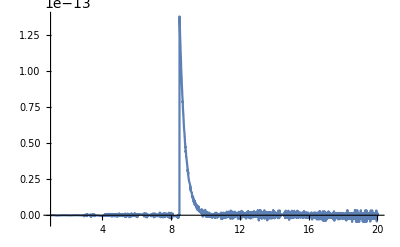

```mathematica
Plot[(-3 J^2+π^2+6 J Log[-1+ⅇ^J]-6 PolyLog[2,ⅇ^-J]+6 PolyLog[2,1-ⅇ^J])/(6 J),{J,1,20}, PlotRange->All]
```

# New term Z(J,omega,omega_0)

```mathematica
p=Integrate[x/J(1/(Exp[x]-1)+1/(Exp[x]+1))(1/(Exp[ω0-x]+1)), {x,-J,+J}, 
Assumptions->J>0&&ω0>0]
f=FullSimplify[p, Assumptions->ω>0&&J>0&&ω0>0]
```

1/(6 (-1+ⅇ^(2 ω0)) J)(-12 ⅈ J π+12 ⅈ ⅇ^ω0 J π+3 π^2-ⅇ^ω0 π^2-12 J Log[-1+ⅇ^J]+12 J Log[1+ⅇ^J]+12 ⅇ^ω0 J Log[-1+ⅇ^(2 J)]-12 ⅇ^ω0 J Log[1+ⅇ^(J-ω0)]-12 ⅇ^ω0 J Log[1+ⅇ^(J+ω0)]+6 PolyLog[2,-ⅇ^J]-18 PolyLog[2,ⅇ^J]+3 PolyLog[2,ⅇ^(2 J)]+6 ⅇ^ω0 PolyLog[2,ⅇ^(2 J)]-12 ⅇ^ω0 PolyLog[2,-ⅇ^(J-ω0)]+12 ⅇ^ω0 PolyLog[2,-ⅇ^-ω0]+12 ⅇ^ω0 PolyLog[2,-ⅇ^ω0]-12 ⅇ^ω0 PolyLog[2,-ⅇ^(J+ω0)])

1/(4 J)ⅇ^-ω0 Csch[ω0] (-4 ⅈ J π+π^2+8 J ArcCoth[ⅇ^J]-8 PolyLog[2,ⅇ^J]+2 (1+ⅇ^ω0) PolyLog[2,ⅇ^(2 J)]-ⅇ^ω0 (-4 ⅈ J π+π^2-4 J ω0+2 ω0^2+4 J Log[1/2 (ⅇ^J+ⅇ^ω0) (1+ⅇ^(J+ω0)) (-1+Coth[J])]+4 PolyLog[2,-ⅇ^(J-ω0)]+4 PolyLog[2,-ⅇ^(J+ω0)]))

```mathematica
1/(4 J)ⅇ^-ω0 Csch[ω0] (-4 ⅈ J π+π^2+8 J ArcCoth[ⅇ^J]-8 PolyLog[2,ⅇ^J]+2 (1+ⅇ^ω0) PolyLog[2,ⅇ^(2 J)]-ⅇ^ω0 (-4 ⅈ J π+π^2-4 J ω0+2 ω0^2+4 J Log[1/2 (ⅇ^J+ⅇ^ω0) (1+ⅇ^(J+ω0)) (-1+Coth[J])]+4 PolyLog[2,-ⅇ^(J-ω0)]+4 PolyLog[2,-ⅇ^(J+ω0)]))/.{J->1/T}
```

1/4 ⅇ^-ω0 T Csch[ω0] (π^2-(4 ⅈ π)/T+(8 ArcCoth[ⅇ^(1/T)])/T-8 PolyLog[2,ⅇ^(1/T)]+2 (1+ⅇ^ω0) PolyLog[2,ⅇ^(2/T)]-ⅇ^ω0 (π^2-(4 ⅈ π)/T-(4 ω0)/T+2 ω0^2+(4 Log[1/2 (ⅇ^(1/T)+ⅇ^ω0) (1+ⅇ^(1/T+ω0)) (-1+Coth[1/T])])/T+4 PolyLog[2,-ⅇ^(1/T-ω0)]+4 PolyLog[2,-ⅇ^(1/T+ω0)]))

```mathematica
Manipulate[Plot[1/4 ⅇ^-ω0 T Csch[ω0] (π^2-(4 ⅈ π)/T+(8 ArcCoth[ⅇ^(1/T)])/T-8 PolyLog[2,ⅇ^(1/T)]+2 (1+ⅇ^ω0) PolyLog[2,ⅇ^(2/T)]-ⅇ^ω0 (π^2-(4 ⅈ π)/T-(4 ω0)/T+2 ω0^2+(4 Log[1/2 (ⅇ^(1/T)+ⅇ^ω0) (1+ⅇ^(1/T+ω0)) (-1+Coth[1/T])])/T+4 PolyLog[2,-ⅇ^(1/T-ω0)]+4 PolyLog[2,-ⅇ^(1/T+ω0)])), {T,0.1,10}, PlotRange->All],{ω0,0.01,10}]
```

```mathematica
p=Integrate[x/J(1/(Exp[x]-1)+1/(Exp[x- ω]+1))1/(Exp[ω0+ω-x]+1), {x,-J,+J}, 
Assumptions->ω>0&&J>0&&ω0>0]
f=FullSimplify[p, Assumptions->ω>0&&J>0&&ω0>0]
```

(6 ⅈ J π-π^2+3 J ω+3 J ω0+6 J Log[-1+ⅇ^J]-3 J Log[ⅇ^J+ⅇ^(ω+ω0)]-3 J Log[1+ⅇ^(J+ω+ω0)]+6 PolyLog[2,ⅇ^J]+3 PolyLog[2,-ⅇ^(-ω-ω0)]-3 PolyLog[2,-ⅇ^(J-ω-ω0)]+3 PolyLog[2,-ⅇ^(ω+ω0)]-3 PolyLog[2,-ⅇ^(J+ω+ω0)])/(3 J+3 ⅇ^(ω+ω0) J)+1/((-1+ⅇ^ω0) J)(J Log[1+ⅇ^(J-ω)]+J Log[1+ⅇ^(J+ω)]-J Log[1+ⅇ^(J-ω-ω0)]-J Log[1+ⅇ^(J+ω+ω0)]+PolyLog[2,-ⅇ^(J-ω)]-PolyLog[2,-ⅇ^-ω]-PolyLog[2,-ⅇ^ω]+PolyLog[2,-ⅇ^(J+ω)]+PolyLog[2,-ⅇ^(-ω-ω0)]-PolyLog[2,-ⅇ^(J-ω-ω0)]+PolyLog[2,-ⅇ^(ω+ω0)]-PolyLog[2,-ⅇ^(J+ω+ω0)])

1/(2 (-1+ⅇ^ω0) (1+ⅇ^(ω+ω0)) J)(2 J^2-4 ⅈ J π-(-1+ⅇ^ω0) π^2+ω^2+2 ⅇ^ω0 J (2 ⅈ π+ω+ω0)+ⅇ^ω0 (-(ω+ω0)^2-ⅇ^ω ω0 (2 ω+ω0))+2 J (Log[2]+2 (-1+ⅇ^ω0) Log[-1+ⅇ^J]-ⅇ^ω0 Log[(ⅇ^J+ⅇ^(ω+ω0)) (1+ⅇ^(J+ω+ω0))]+Log[Cosh[J]+Cosh[ω]]+ⅇ^(ω+ω0) Log[(Cosh[J]+Cosh[ω])/(Cosh[J]+Cosh[ω+ω0])])+4 (-1+ⅇ^ω0) PolyLog[2,ⅇ^J]+2 (1+ⅇ^(ω+ω0)) PolyLog[2,-ⅇ^(J-ω)]+2 (1+ⅇ^(ω+ω0)) PolyLog[2,-ⅇ^(J+ω)]-2 ⅇ^ω0 (1+ⅇ^ω) PolyLog[2,-ⅇ^(J-ω-ω0)]-2 ⅇ^ω0 (1+ⅇ^ω) PolyLog[2,-ⅇ^(J+ω+ω0)])

```mathematica
p=Integrate[x/J(1/(Exp[x]-1)+1/(Exp[x- ω]+1))1/(Exp[ω-ω0-x]+1), {x,-J,+J}, 
Assumptions->ω>0&&J>0&&ω0>0]
f2=FullSimplify[p, Assumptions->ω>0&&J>0&&ω0>0]
```

1/(3 J)ⅇ^ω0 ((6 ⅈ J π-π^2+3 J ω+3 J ω0+6 J Log[-1+ⅇ^J]-3 J Log[ⅇ^(J+ω)+ⅇ^ω0]-3 J Log[ⅇ^ω+ⅇ^(J+ω0)]+6 PolyLog[2,ⅇ^J]+3 PolyLog[2,-ⅇ^(ω-ω0)]-3 PolyLog[2,-ⅇ^(J+ω-ω0)]+3 PolyLog[2,-ⅇ^(-ω+ω0)]-3 PolyLog[2,-ⅇ^(J-ω+ω0)])/(ⅇ^ω+ⅇ^ω0)+1/(-1+ⅇ^ω0)3 (-J Log[ⅇ^J+ⅇ^ω]-J Log[1+ⅇ^(J+ω)]+J Log[1+ⅇ^(J+ω-ω0)]+J Log[ⅇ^ω+ⅇ^(J+ω0)]-PolyLog[2,-ⅇ^(J-ω)]+PolyLog[2,-ⅇ^-ω]+PolyLog[2,-ⅇ^ω]-PolyLog[2,-ⅇ^(J+ω)]-PolyLog[2,-ⅇ^(ω-ω0)]+PolyLog[2,-ⅇ^(J+ω-ω0)]-PolyLog[2,-ⅇ^(-ω+ω0)]+PolyLog[2,-ⅇ^(J-ω+ω0)]))

1/(2 J)ⅇ^ω0 (-(π^2+(ω-ω0)^2-2 J (2 ⅈ π+ω+ω0)-4 J Log[-1+ⅇ^J]+2 J Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))]-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)])/(ⅇ^ω+ⅇ^ω0)+(ω0 (-2 (J+ω)+ω0)+2 J (-Log[(ⅇ^J+ⅇ^ω) (1+ⅇ^(J+ω))]+Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)])/(-1+ⅇ^ω0))

```mathematica
FullSimplify[f+f2, Assumptions->ω>0&&J>0&&ω0>0]
```

1/(2 J)(ⅇ^ω0 (-(π^2+(ω-ω0)^2-2 J (2 ⅈ π+ω+ω0)-4 J Log[-1+ⅇ^J]+2 J Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))]-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)])/(ⅇ^ω+ⅇ^ω0)+(ω0 (-2 (J+ω)+ω0)+2 J (-Log[(ⅇ^J+ⅇ^ω) (1+ⅇ^(J+ω))]+Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)])/(-1+ⅇ^ω0))+1/((-1+ⅇ^ω0) (1+ⅇ^(ω+ω0)))(2 J^2-4 ⅈ J π-(-1+ⅇ^ω0) π^2+ω^2+2 ⅇ^ω0 J (2 ⅈ π+ω+ω0)+ⅇ^ω0 (-(ω+ω0)^2-ⅇ^ω ω0 (2 ω+ω0))+2 J (Log[2]+2 (-1+ⅇ^ω0) Log[-1+ⅇ^J]-ⅇ^ω0 Log[(ⅇ^J+ⅇ^(ω+ω0)) (1+ⅇ^(J+ω+ω0))]+Log[Cosh[J]+Cosh[ω]]+ⅇ^(ω+ω0) Log[(Cosh[J]+Cosh[ω])/(Cosh[J]+Cosh[ω+ω0])])+4 (-1+ⅇ^ω0) PolyLog[2,ⅇ^J]+2 (1+ⅇ^(ω+ω0)) PolyLog[2,-ⅇ^(J-ω)]+2 (1+ⅇ^(ω+ω0)) PolyLog[2,-ⅇ^(J+ω)]-2 ⅇ^ω0 (1+ⅇ^ω) PolyLog[2,-ⅇ^(J-ω-ω0)]-2 ⅇ^ω0 (1+ⅇ^ω) PolyLog[2,-ⅇ^(J+ω+ω0)]))

## test 1 for simplification

```mathematica
Simplify[-1/(2 J)((ⅇ^(2 ω) ((2 (J+ω)-ω0) ω0+2 J (Log[(ⅇ^J+ⅇ^ω) (1+ⅇ^(J+ω))]-Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])+2 PolyLog[2,-ⅇ^(J-ω)]+2 PolyLog[2,-ⅇ^(J+ω)]-2 PolyLog[2,-ⅇ^(J+ω-ω0)]-2 PolyLog[2,-ⅇ^(J-ω+ω0)]))/(ⅇ^(2 ω)-ⅇ^ω0)+(ⅇ^ω (-4 ⅈ J π+π^2+(ω-ω0)^2-2 J (ω+ω0)+2 J (-2 Log[-1+ⅇ^J]+Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)]))/(ⅇ^ω+ⅇ^ω0)+(2 J^2-4 ⅈ J π+π^2+(ω+ω0)^2+J Log[4]+2 J (-2 Log[-1+ⅇ^J]+Log[Cosh[J]+Cosh[ω+ω0]])-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])/(1+ⅇ^(ω+ω0))+(2 ω ω0+ω0^2+2 J Log[(Cosh[J]+Cosh[ω+ω0])/(Cosh[J]+Cosh[ω])]-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])/(-1+ⅇ^ω0))+1/(2 J)(((2 (J+ω)-ω0) ω0+2 J (Log[(ⅇ^J+ⅇ^ω) (1+ⅇ^(J+ω))]-Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])+2 PolyLog[2,-ⅇ^(J-ω)]+2 PolyLog[2,-ⅇ^(J+ω)]-2 PolyLog[2,-ⅇ^(J+ω-ω0)]-2 PolyLog[2,-ⅇ^(J-ω+ω0)])/(1-ⅇ^(ω0-2 ω))+(-4 ⅈ J π+π^2+(ω-ω0)^2-2 J (ω+ω0)+2 J (-2 Log[-1+ⅇ^J]+Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)])/(1+ⅇ^(ω0-ω))+(2 J^2-4 ⅈ J π+π^2+(ω+ω0)^2+J Log[4]+2 J (-2 Log[-1+ⅇ^J]+Log[Cosh[J]+Cosh[ω+ω0]])-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])/(1+ⅇ^(ω+ω0))+(2 ω ω0+ω0^2+2 J Log[(Cosh[J]+Cosh[ω+ω0])/(Cosh[J]+Cosh[ω])]-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])/(-1+ⅇ^ω0))]
```

0

## test 2 for simplification

```mathematica
Simplify[-1/(2 J)((ⅇ^(2 ω) ((2 (J+ω)-ω0) ω0+2 J (Log[(ⅇ^J+ⅇ^ω) (1+ⅇ^(J+ω))]-Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])+2 PolyLog[2,-ⅇ^(J-ω)]+2 PolyLog[2,-ⅇ^(J+ω)]-2 PolyLog[2,-ⅇ^(J+ω-ω0)]-2 PolyLog[2,-ⅇ^(J-ω+ω0)]))/(ⅇ^(2 ω)-ⅇ^ω0)+(ⅇ^ω (-4 ⅈ J π+π^2+(ω-ω0)^2-2 J (ω+ω0)+2 J (-2 Log[-1+ⅇ^J]+Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)]))/(ⅇ^ω+ⅇ^ω0)+(2 J^2-4 ⅈ J π+π^2+(ω+ω0)^2+J Log[4]+2 J (-2 Log[-1+ⅇ^J]+Log[Cosh[J]+Cosh[ω+ω0]])-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])/(1+ⅇ^(ω+ω0))+(2 ω ω0+ω0^2+2 J Log[(Cosh[J]+Cosh[ω+ω0])/(Cosh[J]+Cosh[ω])]-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])/(-1+ⅇ^ω0))+1/(2 J)((2 ω ω0-ω0^2-2 J Log[(Cosh[J]+Cosh[ω-ω0])/(Cosh[J]+Cosh[ω])]+2 PolyLog[2,-ⅇ^(J-ω)]+2 PolyLog[2,-ⅇ^(J+ω)]-2 PolyLog[2,-ⅇ^(J+ω-ω0)]-2 PolyLog[2,-ⅇ^(J-ω+ω0)])/(1-ⅇ^(ω0-2 ω))+(-4 ⅈ J π+π^2+(ω-ω0)^2-2 J (ω+ω0)+2 J (-2 Log[-1+ⅇ^J]+Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)])/(1+ⅇ^(ω0-ω))+(2 J^2-4 ⅈ J π+π^2+(ω+ω0)^2+J Log[4]+2 J (-2 Log[-1+ⅇ^J]+Log[Cosh[J]+Cosh[ω+ω0]])-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])/(1+ⅇ^(ω+ω0))+(2 ω ω0+ω0^2+2 J Log[(Cosh[J]+Cosh[ω+ω0])/(Cosh[J]+Cosh[ω])]-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])/(-1+ⅇ^ω0)),Assumptions->ω>0&&J>0&&ω0>0]
```

0

## Test 3 for simplification

```mathematica
Simplify[-1/(2 J)((ⅇ^(2 ω) ((2 (J+ω)-ω0) ω0+2 J (Log[(ⅇ^J+ⅇ^ω) (1+ⅇ^(J+ω))]-Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])+2 PolyLog[2,-ⅇ^(J-ω)]+2 PolyLog[2,-ⅇ^(J+ω)]-2 PolyLog[2,-ⅇ^(J+ω-ω0)]-2 PolyLog[2,-ⅇ^(J-ω+ω0)]))/(ⅇ^(2 ω)-ⅇ^ω0)+(ⅇ^ω (-4 ⅈ J π+π^2+(ω-ω0)^2-2 J (ω+ω0)+2 J (-2 Log[-1+ⅇ^J]+Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)]))/(ⅇ^ω+ⅇ^ω0)+(2 J^2-4 ⅈ J π+π^2+(ω+ω0)^2+J Log[4]+2 J (-2 Log[-1+ⅇ^J]+Log[Cosh[J]+Cosh[ω+ω0]])-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])/(1+ⅇ^(ω+ω0))+(2 ω ω0+ω0^2+2 J Log[(Cosh[J]+Cosh[ω+ω0])/(Cosh[J]+Cosh[ω])]-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])/(-1+ⅇ^ω0))+1/(2 J)((2 ω ω0-ω0^2-2 J Log[(Cosh[J]+Cosh[ω-ω0])/(Cosh[J]+Cosh[ω])]+2 PolyLog[2,-ⅇ^(J-ω)]+2 PolyLog[2,-ⅇ^(J+ω)]-2 PolyLog[2,-ⅇ^(J+ω-ω0)]-2 PolyLog[2,-ⅇ^(J-ω+ω0)])/(1-ⅇ^(ω0-2 ω))+(-4 ⅈ J π+π^2+(ω-ω0)^2-2 J (ω+ω0)+2 J (-2 Log[-1+ⅇ^J]+Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)])/(1+ⅇ^(ω0-ω))+(2 J^2-4 ⅈ J π+π^2+(ω+ω0)^2+J Log[4]+2 J (-2 Log[-1+ⅇ^J]+Log[Cosh[J]+Cosh[ω+ω0]])-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])/(1+ⅇ^(ω+ω0))+(2 ω ω0+ω0^2+2 J Log[(Cosh[J]+Cosh[ω+ω0])/(Cosh[J]+Cosh[ω])]-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])/(-1+ⅇ^ω0)),Assumptions->ω>0&&J>0&&ω0>0]
```

0

## aside for simplification

```mathematica
(2 J^2-4 ⅈ J π+π^2+(ω)^2+J Log[4]+2 J (-2 Log[-1+ⅇ^J]+Log[Cosh[J]+Cosh[ω]])-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω)]+2 PolyLog[2,-ⅇ^(J+ω)])/J
```

```mathematica
(2 J^2-4 ⅈ J π+π^2+ω^2+J Log[4]+2 J (-2 Log[-1+ⅇ^J]+Log[Cosh[J]+Cosh[ω]])-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω)]+2 PolyLog[2,-ⅇ^(J+ω)])/J-(-J^2/2+2 J ω-J Log[(1+ⅇ^(-J+ω)) (1+ⅇ^(J+ω))]+PolyLog[2,-ⅇ^(-J-ω)]-PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,1-ⅇ^J])/J
```

# Evaluating variables

```mathematica
-1/(2 J)((ⅇ^(2 ω) ((2 (J+ω)-ω0) ω0+2 J (Log[(ⅇ^J+ⅇ^ω) (1+ⅇ^(J+ω))]-Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])+2 PolyLog[2,-ⅇ^(J-ω)]+2 PolyLog[2,-ⅇ^(J+ω)]-2 PolyLog[2,-ⅇ^(J+ω-ω0)]-2 PolyLog[2,-ⅇ^(J-ω+ω0)]))/(ⅇ^(2 ω)-ⅇ^ω0)+(ⅇ^ω (-4 ⅈ J π+π^2+(ω-ω0)^2-2 J (ω+ω0)+2 J (-2 Log[-1+ⅇ^J]+Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)]))/(ⅇ^ω+ⅇ^ω0)+(2 J^2-4 ⅈ J π+π^2+(ω+ω0)^2+J Log[4]+2 J (-2 Log[-1+ⅇ^J]+Log[Cosh[J]+Cosh[ω+ω0]])-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])/(1+ⅇ^(ω+ω0))+(2 ω ω0+ω0^2+2 J Log[(Cosh[J]+Cosh[ω+ω0])/(Cosh[J]+Cosh[ω])]-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])/(-1+ⅇ^ω0))/.{J->1/T,ω0->ω0/T,ω->ω/T}
```

-1/2 T ((ⅇ^((2 ω)/T) ((ω0 (2 (1/T+ω/T)-ω0/T))/T+(2 (Log[(ⅇ^(1/T)+ⅇ^(ω/T)) (1+ⅇ^(1/T+ω/T))]-Log[(ⅇ^(1/T+ω/T)+ⅇ^(ω0/T)) (ⅇ^(ω/T)+ⅇ^(1/T+ω0/T))]))/T+2 PolyLog[2,-ⅇ^(1/T-ω/T)]+2 PolyLog[2,-ⅇ^(1/T+ω/T)]-2 PolyLog[2,-ⅇ^(1/T+ω/T-ω0/T)]-2 PolyLog[2,-ⅇ^(1/T-ω/T+ω0/T)]))/(ⅇ^((2 ω)/T)-ⅇ^(ω0/T))+(ⅇ^(ω/T) (π^2-(4 ⅈ π)/T+(ω/T-ω0/T)^2-(2 (ω/T+ω0/T))/T+(2 (-2 Log[-1+ⅇ^(1/T)]+Log[(ⅇ^(1/T+ω/T)+ⅇ^(ω0/T)) (ⅇ^(ω/T)+ⅇ^(1/T+ω0/T))]))/T-4 PolyLog[2,ⅇ^(1/T)]+2 PolyLog[2,-ⅇ^(1/T+ω/T-ω0/T)]+2 PolyLog[2,-ⅇ^(1/T-ω/T+ω0/T)]))/(ⅇ^(ω/T)+ⅇ^(ω0/T))+(π^2+2/T^2-(4 ⅈ π)/T+(ω/T+ω0/T)^2+Log[4]/T+(2 (-2 Log[-1+ⅇ^(1/T)]+Log[Cosh[1/T]+Cosh[ω/T+ω0/T]]))/T-4 PolyLog[2,ⅇ^(1/T)]+2 PolyLog[2,-ⅇ^(1/T-ω/T-ω0/T)]+2 PolyLog[2,-ⅇ^(1/T+ω/T+ω0/T)])/(1+ⅇ^(ω/T+ω0/T))+((2 ω ω0)/T^2+ω0^2/T^2+(2 Log[(Cosh[1/T]+Cosh[ω/T+ω0/T])/(Cosh[1/T]+Cosh[ω/T])])/T-2 PolyLog[2,-ⅇ^(1/T-ω/T)]-2 PolyLog[2,-ⅇ^(1/T+ω/T)]+2 PolyLog[2,-ⅇ^(1/T-ω/T-ω0/T)]+2 PolyLog[2,-ⅇ^(1/T+ω/T+ω0/T)])/(-1+ⅇ^(ω0/T)))

```mathematica
-1/(2 J)((ⅇ^(2 ω) ((2 (J+ω)-ω0) ω0+2 J (Log[(ⅇ^J+ⅇ^ω) (1+ⅇ^(J+ω))]-Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])+2 PolyLog[2,-ⅇ^(J-ω)]+2 PolyLog[2,-ⅇ^(J+ω)]-2 PolyLog[2,-ⅇ^(J+ω-ω0)]-2 PolyLog[2,-ⅇ^(J-ω+ω0)]))/(ⅇ^(2 ω)-ⅇ^ω0)+(ⅇ^ω (-4 ⅈ J π+π^2+(ω-ω0)^2-2 J (ω+ω0)+2 J (-2 Log[-1+ⅇ^J]+Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)]))/(ⅇ^ω+ⅇ^ω0)+(2 J^2-4 ⅈ J π+π^2+(ω+ω0)^2+J Log[4]+2 J (-2 Log[-1+ⅇ^J]+Log[Cosh[J]+Cosh[ω+ω0]])-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])/(1+ⅇ^(ω+ω0))+(2 ω ω0+ω0^2+2 J Log[(Cosh[J]+Cosh[ω+ω0])/(Cosh[J]+Cosh[ω])]-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])/(-1+ⅇ^ω0))/.{J->1/T,ω0->ω0/T,ω->0}
```

-1/2 T (((ω0 (2/T-ω0/T))/T+(2 (Log[(1+ⅇ^(1/T))^2]-Log[(ⅇ^(1/T)+ⅇ^(ω0/T)) (1+ⅇ^(1/T+ω0/T))]))/T+4 PolyLog[2,-ⅇ^(1/T)]-2 PolyLog[2,-ⅇ^(1/T-ω0/T)]-2 PolyLog[2,-ⅇ^(1/T+ω0/T)])/(1-ⅇ^(ω0/T))+(ω0^2/T^2+(2 Log[(Cosh[1/T]+Cosh[ω0/T])/(1+Cosh[1/T])])/T-4 PolyLog[2,-ⅇ^(1/T)]+2 PolyLog[2,-ⅇ^(1/T-ω0/T)]+2 PolyLog[2,-ⅇ^(1/T+ω0/T)])/(-1+ⅇ^(ω0/T))+(π^2-(4 ⅈ π)/T-(2 ω0)/T^2+ω0^2/T^2+(2 (-2 Log[-1+ⅇ^(1/T)]+Log[(ⅇ^(1/T)+ⅇ^(ω0/T)) (1+ⅇ^(1/T+ω0/T))]))/T-4 PolyLog[2,ⅇ^(1/T)]+2 PolyLog[2,-ⅇ^(1/T-ω0/T)]+2 PolyLog[2,-ⅇ^(1/T+ω0/T)])/(1+ⅇ^(ω0/T))+(π^2+2/T^2-(4 ⅈ π)/T+ω0^2/T^2+Log[4]/T+(2 (-2 Log[-1+ⅇ^(1/T)]+Log[Cosh[1/T]+Cosh[ω0/T]]))/T-4 PolyLog[2,ⅇ^(1/T)]+2 PolyLog[2,-ⅇ^(1/T-ω0/T)]+2 PolyLog[2,-ⅇ^(1/T+ω0/T)])/(1+ⅇ^(ω0/T)))

```mathematica
Manipulate[Plot[-1/2 T (((ω0 (2/T-ω0/T))/T+(2 (Log[(1+ⅇ^(1/T))^2]-Log[(ⅇ^(1/T)+ⅇ^(ω0/T)) (1+ⅇ^(1/T+ω0/T))]))/T+4 PolyLog[2,-ⅇ^(1/T)]-2 PolyLog[2,-ⅇ^(1/T-ω0/T)]-2 PolyLog[2,-ⅇ^(1/T+ω0/T)])/(1-ⅇ^(ω0/T))+(ω0^2/T^2+(2 Log[(Cosh[1/T]+Cosh[ω0/T])/(1+Cosh[1/T])])/T-4 PolyLog[2,-ⅇ^(1/T)]+2 PolyLog[2,-ⅇ^(1/T-ω0/T)]+2 PolyLog[2,-ⅇ^(1/T+ω0/T)])/(-1+ⅇ^(ω0/T))+(π^2-(4 ⅈ π)/T-(2 ω0)/T^2+ω0^2/T^2+(2 (-2 Log[-1+ⅇ^(1/T)]+Log[(ⅇ^(1/T)+ⅇ^(ω0/T)) (1+ⅇ^(1/T+ω0/T))]))/T-4 PolyLog[2,ⅇ^(1/T)]+2 PolyLog[2,-ⅇ^(1/T-ω0/T)]+2 PolyLog[2,-ⅇ^(1/T+ω0/T)])/(1+ⅇ^(ω0/T))+(π^2+2/T^2-(4 ⅈ π)/T+ω0^2/T^2+Log[4]/T+(2 (-2 Log[-1+ⅇ^(1/T)]+Log[Cosh[1/T]+Cosh[ω0/T]]))/T-4 PolyLog[2,ⅇ^(1/T)]+2 PolyLog[2,-ⅇ^(1/T-ω0/T)]+2 PolyLog[2,-ⅇ^(1/T+ω0/T)])/(1+ⅇ^(ω0/T))), {T,0.1,10}, PlotRange->All],{ω0,0.01,10}]
```

```mathematica
FullSimplify[(Log[ⅇ^ω0(ⅇ^J+ⅇ^ω) (1+ⅇ^(J+ω))]-Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])+Log[(Cosh[J]+Cosh[ω-ω0])/(Cosh[J]+Cosh[ω])],Assumptions->ω>0&&J>0&&ω0>0]
```

0

```mathematica
((ⅇ^J+ⅇ^ω) (1+ⅇ^(J+ω)))/((ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0)))
```

```mathematica
ExpToTrig[(ⅇ^ω0(ⅇ^J+ⅇ^ω) (1+ⅇ^(J+ω)))/((ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0)))]
```

((Cosh[J]+Cosh[ω]+Sinh[J]+Sinh[ω]) (1+Cosh[J+ω]+Sinh[J+ω]) (Cosh[ω0]+Sinh[ω0]))/((Cosh[J+ω]+Cosh[ω0]+Sinh[J+ω]+Sinh[ω0]) (Cosh[ω]+Cosh[J+ω0]+Sinh[ω]+Sinh[J+ω0]))

```mathematica
Expand[(2 (J+ω)-ω0) ω0]
```

2 J ω0+2 ω ω0-ω0^2

```mathematica
FullSimplify[(1/(Exp[x]-1)+1/(Exp[x- ω]+1))1/(Exp[ω0-x]+1)]
```

(1/(-1+ⅇ^x)+1/(1+ⅇ^(x-ω)))/(1+ⅇ^(-x+ω0))

## Relevant integrals

```mathematica
Integrate[x 1/(Exp[x]-1)1/(Exp[ω0p-x]+1), {x,-J,J}, Assumptions->J>0&&ω0p∈Reals]
```

-(-4 ⅈ J π+π^2-2 J ω0p+ω0p^2-4 J Log[-1+ⅇ^J]+2 J Log[(ⅇ^J+ⅇ^ω0p) (1+ⅇ^(J+ω0p))]-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω0p)]+2 PolyLog[2,-ⅇ^(J+ω0p)])/(2 (1+ⅇ^ω0p))

```mathematica
Integrate[x 1/(Exp[x- ω]+1)1/(Exp[ω0p-x]+1), {x,-J,J}, Assumptions->J>0&&ω0p∈Reals&& ω∈Reals]
```

(ⅇ^ω (-ω^2/2+ω0p^2/2-J Log[(1+ⅇ^(J-ω)) (1+ⅇ^(J+ω))]+J Log[(1+ⅇ^(J-ω0p)) (1+ⅇ^(J+ω0p))]-PolyLog[2,-ⅇ^(J-ω)]-PolyLog[2,-ⅇ^(J+ω)]+PolyLog[2,-ⅇ^(J-ω0p)]+PolyLog[2,-ⅇ^(J+ω0p)]))/(ⅇ^ω-ⅇ^ω0p)

## End of relevan integrals

```mathematica
FullSimplify[-(-4 ⅈ J π+π^2-2 J ω0p+ω0p^2-4 J Log[-1+ⅇ^J]+2 J Log[(ⅇ^J+ⅇ^ω0p) (1+ⅇ^(J+ω0p))]-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω0p)]+2 PolyLog[2,-ⅇ^(J+ω0p)])/(2 (1+ⅇ^ω0p)), Assumptions->J>0&&ω0p∈Reals&& ω∈Reals]
```

-(-4 ⅈ J π+π^2-2 J ω0p+ω0p^2-4 J Log[-1+ⅇ^J]+2 J Log[(ⅇ^J+ⅇ^ω0p) (1+ⅇ^(J+ω0p))]-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω0p)]+2 PolyLog[2,-ⅇ^(J+ω0p)])/(2 (1+ⅇ^ω0p))

```mathematica
Assuming[J>0&&ω0p∈Reals&& ω∈Reals,Simplify[Refine[Re[ComplexExpand[-(-4 ⅈ J π+π^2-2 J ω0p+ω0p^2-4 J Log[-1+ⅇ^J]+2 J Log[(ⅇ^J+ⅇ^ω0p) (1+ⅇ^(J+ω0p))]-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω0p)]+2 PolyLog[2,-ⅇ^(J+ω0p)])/(2 (1+ⅇ^ω0p))]],J>0&&ω0p∈Reals&& ω∈Reals],Element[ω,Reals]]]
```

-(π^2-2 J ω0p+ω0p^2-4 J Log[-1+ⅇ^J]+2 J Log[ⅇ^J+ⅇ^ω0p]+2 J Log[1+ⅇ^(J+ω0p)]+2 PolyLog[2,-ⅇ^(J-ω0p)]+2 PolyLog[2,-ⅇ^(J+ω0p)]-4 Re[PolyLog[2,ⅇ^J]])/(2+2 ⅇ^ω0p)

```mathematica
Manipulate[Plot[{-(π^2-2 J ω0p+ω0p^2-4 J Log[-1+ⅇ^J]+2 J Log[ⅇ^J+ⅇ^ω0p]+2 J Log[1+ⅇ^(J+ω0p)]+2 PolyLog[2,-ⅇ^(J-ω0p)]+2 PolyLog[2,-ⅇ^(J+ω0p)]-4 Re[PolyLog[2,ⅇ^J]])/(2+2 ⅇ^ω0p),-(-4 ⅈ J π+π^2-2 J ω0p+ω0p^2-4 J Log[-1+ⅇ^J]+2 J Log[(ⅇ^J+ⅇ^ω0p) (1+ⅇ^(J+ω0p))]-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω0p)]+2 PolyLog[2,-ⅇ^(J+ω0p)])/(2 (1+ⅇ^ω0p))},{J,0,10}],{ ω0p,-1,1}]
```

```mathematica
Manipulate[Plot[{-(π^2-2 J ω0p+ω0p^2-4 J Log[-1+ⅇ^J]+2 J Log[ⅇ^J+ⅇ^ω0p]+2 J Log[1+ⅇ^(J+ω0p)]+2 PolyLog[2,-ⅇ^(J-ω0p)]+2 PolyLog[2,-ⅇ^(J+ω0p)]-4 PolyLog[2,ⅇ^J])/(2+2 ⅇ^ω0p),-(-4 ⅈ J π+π^2-2 J ω0p+ω0p^2-4 J Log[-1+ⅇ^J]+2 J Log[(ⅇ^J+ⅇ^ω0p) (1+ⅇ^(J+ω0p))]-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω0p)]+2 PolyLog[2,-ⅇ^(J+ω0p)])/(2 (1+ⅇ^ω0p))},{J,0,10}],{ ω0p,-1,1}]
```

```mathematica
N[(π^2-2 J ω0p+ω0p^2-4 J Log[-1+ⅇ^J]+2 J Log[ⅇ^J+ⅇ^ω0p]+2 J Log[1+ⅇ^(J+ω0p)]+2 PolyLog[2,-ⅇ^(J-ω0p)]+2 PolyLog[2,-ⅇ^(J+ω0p)]-4 PolyLog[2,ⅇ^J])/(2+2 ⅇ^ω0p)/.{ω0p->1,J->1}]
```

-0.518086+1.68981 ⅈ

```mathematica
N[(-4 ⅈ J π+π^2-2 J ω0p+ω0p^2-4 J Log[-1+ⅇ^J]+2 J Log[(ⅇ^J+ⅇ^ω0p) (1+ⅇ^(J+ω0p))]-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω0p)]+2 PolyLog[2,-ⅇ^(J+ω0p)])/(2 (1+ⅇ^ω0p))/.{ω0p->1,J->1}]
```

-0.518086+0. ⅈ

```mathematica
N[(π^2-2 J ω0p+ω0p^2-4 J Log[-1+ⅇ^J]+2 J Log[ⅇ^J+ⅇ^ω0p]+2 J Log[1+ⅇ^(J+ω0p)]+2 PolyLog[2,-ⅇ^(J-ω0p)]+2 PolyLog[2,-ⅇ^(J+ω0p)]-4())/(2+2 ⅇ^ω0p)/.{ω0p->1,J->1}]
```

0.542813

```mathematica
FullSimplify[2 J Log[(Cosh[J]+Cosh[ω0p])/(-1+Cosh[J])] -(-2 J ω0p-4 J Log[-1+ⅇ^J]+2 J Log[ⅇ^J+ⅇ^ω0p]+2 J Log[1+ⅇ^(J+ω0p)]),,Assumptions->J>0&&ω0p>0]
```

0

```mathematica
N[(π^2+ω0p^2+ 2 J Log[(Cosh[J]+Cosh[ω0p])/(-1+Cosh[J])]+2 PolyLog[2,-ⅇ^(J-ω0p)]+2 PolyLog[2,-ⅇ^(J+ω0p)]-4 PolyLog[2,ⅇ^J])/(2+2 ⅇ^ω0p)/.{ω0p->1,J->1}]
```

-0.518086+1.68981 ⅈ

```mathematica
N[(π^2+ω0p^2+ 2 J Log[(Cosh[J]+Cosh[ω0p])/(-1+Cosh[J])]+2 PolyLog[2,-ⅇ^(J-ω0p)]+2 PolyLog[2,-ⅇ^(J+ω0p)]-4 (-1/2 J^2+π^2/3- PolyLog[2,ⅇ^-J]))/(2+2 ⅇ^ω0p)/.{ω0p->1,J->1}]
```

-0.518086

```mathematica
FullSimplify[(π^2+ω0p^2+ 2 J Log[(Cosh[J]+Cosh[ω0p])/(-1+Cosh[J])]+2 PolyLog[2,-ⅇ^(J-ω0p)]+2 PolyLog[2,-ⅇ^(J+ω0p)]-4 (-1/2 J^2+π^2/3- PolyLog[2,ⅇ^-J]))/(2+2 ⅇ^ω0p),Assumptions->J>0&&ω0p>0]
```

(6 J^2-π^2+3 ω0p^2+6 J Log[(Cosh[J]+Cosh[ω0p])/(-1+Cosh[J])]+12 PolyLog[2,ⅇ^-J]+6 PolyLog[2,-ⅇ^(J-ω0p)]+6 PolyLog[2,-ⅇ^(J+ω0p)])/(6+6 ⅇ^ω0p)

```mathematica
FullSimplify[(Cosh[J]+Cosh[ω0p])/(-1+Cosh[J])Exp[J],,Assumptions->J>0&&ω0p>0]
```

(ⅇ^J (Cosh[J]+Cosh[ω0p]))/(-1+Cosh[J])

## the real part of polylog

```mathematica
4 (-1/2 J^2+π^2/3- PolyLog[2,ⅇ^-J])==Re[4 PolyLog[2,ⅇ^J]]
```

## test simplified integrals

```mathematica
OG1=-(-4 ⅈ J π+π^2-2 J ω0p+ω0p^2-4 J Log[-1+ⅇ^J]+2 J Log[(ⅇ^J+ⅇ^ω0p) (1+ⅇ^(J+ω0p))]-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω0p)]+2 PolyLog[2,-ⅇ^(J+ω0p)])/(2 (1+ⅇ^ω0p))
```

-(-4 ⅈ J π+π^2-2 J ω0p+ω0p^2-4 J Log[-1+ⅇ^J]+2 J Log[(ⅇ^J+ⅇ^ω0p) (1+ⅇ^(J+ω0p))]-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω0p)]+2 PolyLog[2,-ⅇ^(J+ω0p)])/(2 (1+ⅇ^ω0p))

```mathematica
SIMP1=-(6 J^2-π^2+3 ω0p^2+6 J Log[(Cosh[J]+Cosh[ω0p])/(-1+Cosh[J])]+12 PolyLog[2,ⅇ^-J]+6 PolyLog[2,-ⅇ^(J-ω0p)]+6 PolyLog[2,-ⅇ^(J+ω0p)])/(6+6 ⅇ^ω0p)
```

-(6 J^2-π^2+3 ω0p^2+6 J Log[(Cosh[J]+Cosh[ω0p])/(-1+Cosh[J])]+12 PolyLog[2,ⅇ^-J]+6 PolyLog[2,-ⅇ^(J-ω0p)]+6 PolyLog[2,-ⅇ^(J+ω0p)])/(6+6 ⅇ^ω0p)

```mathematica
FullSimplify[OG1-SIMP1, Assumptions->J>0&&ω0p>0]
```

0

```mathematica
Manipulate[Plot[-(2 J^2-4 ⅈ J π+π^2+ω0p^2-4 J Log[-1+ⅇ^J]+2 J Log[2 (Cosh[J]+Cosh[ω0p])]-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J-ω0p)]+2 PolyLog[2,-ⅇ^(J+ω0p)])/(1+ⅇ^ω0p),{J,0,10}],{ω0p,-10,10}]
```

```mathematica
OG2=(ⅇ^ω (-ω^2/2+ω0p^2/2-J Log[(1+ⅇ^(J-ω)) (1+ⅇ^(J+ω))]+J Log[(1+ⅇ^(J-ω0p)) (1+ⅇ^(J+ω0p))]-PolyLog[2,-ⅇ^(J-ω)]-PolyLog[2,-ⅇ^(J+ω)]+PolyLog[2,-ⅇ^(J-ω0p)]+PolyLog[2,-ⅇ^(J+ω0p)]))/(ⅇ^ω-ⅇ^ω0p)
```

(ⅇ^ω (-ω^2/2+ω0p^2/2-J Log[(1+ⅇ^(J-ω)) (1+ⅇ^(J+ω))]+J Log[(1+ⅇ^(J-ω0p)) (1+ⅇ^(J+ω0p))]-PolyLog[2,-ⅇ^(J-ω)]-PolyLog[2,-ⅇ^(J+ω)]+PolyLog[2,-ⅇ^(J-ω0p)]+PolyLog[2,-ⅇ^(J+ω0p)]))/(ⅇ^ω-ⅇ^ω0p)

```mathematica
SIMP2=((ω0p^2-ω^2)/2+J Log[(Cosh[J]+Cosh[ω0p])/(Cosh[J]+Cosh[ω])]-PolyLog[2,-ⅇ^(J-ω)]-PolyLog[2,-ⅇ^(J+ω)]+PolyLog[2,-ⅇ^(J-ω0p)]+PolyLog[2,-ⅇ^(J+ω0p)])/(1-ⅇ^(ω0p-ω))
```

(1/2 (-ω^2+ω0p^2)+J Log[(Cosh[J]+Cosh[ω0p])/(Cosh[J]+Cosh[ω])]-PolyLog[2,-ⅇ^(J-ω)]-PolyLog[2,-ⅇ^(J+ω)]+PolyLog[2,-ⅇ^(J-ω0p)]+PolyLog[2,-ⅇ^(J+ω0p)])/(1-ⅇ^(-ω+ω0p))

```mathematica
FullSimplify[OG2-SIMP2, Assumptions->J>0&&ω0p>0&&ω>0]
```

(ⅇ^ω J (Log[(1+ⅇ^(J-ω0p)) (1+ⅇ^(J+ω0p)) (Cosh[J]+Cosh[ω])]-Log[(1+ⅇ^(J-ω)) (1+ⅇ^(J+ω)) (Cosh[J]+Cosh[ω0p])]))/(ⅇ^ω-ⅇ^ω0p)

```mathematica
Manipulate[Plot[(ⅇ^ω J (Log[(1+ⅇ^(J-ω0p)) (1+ⅇ^(J+ω0p)) (Cosh[J]+Cosh[ω])]-Log[(1+ⅇ^(J-ω)) (1+ⅇ^(J+ω)) (Cosh[J]+Cosh[ω0p])]))/(ⅇ^ω-ⅇ^ω0p),{J,0,10}],{ω0p,-10,10},{ω,-10,10}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/ⅇ^10 encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/ⅇ^10 encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/ⅇ^10 encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
-J Log[]+J Log[((1+ⅇ^(J-ω0p)) (1+ⅇ^(J+ω0p)))/((1+ⅇ^(J-ω)) (1+ⅇ^(J+ω)))]
```

```mathematica
FullSimplify[((1+ⅇ^(J-ω0p)) (1+ⅇ^(J+ω0p)))/((1+ⅇ^(J-ω)) (1+ⅇ^(J+ω)))]
```

(Cosh[J]+Cosh[ω0p])/(Cosh[J]+Cosh[ω])

# Final test for simplification of Z

```mathematica
f1=SIMP1/.ω0p->ω0+ω
```

-1/(6+6 ⅇ^(ω+ω0))(6 J^2-π^2+3 (ω+ω0)^2+6 J Log[(Cosh[J]+Cosh[ω+ω0])/(-1+Cosh[J])]+12 PolyLog[2,ⅇ^-J]+6 PolyLog[2,-ⅇ^(J-ω-ω0)]+6 PolyLog[2,-ⅇ^(J+ω+ω0)])

```mathematica
f2=SIMP1/.ω0p->-ω0+ω
```

-1/(6+6 ⅇ^(ω-ω0))(6 J^2-π^2+3 (ω-ω0)^2+6 J Log[(Cosh[J]+Cosh[ω-ω0])/(-1+Cosh[J])]+12 PolyLog[2,ⅇ^-J]+6 PolyLog[2,-ⅇ^(J+ω-ω0)]+6 PolyLog[2,-ⅇ^(J-ω+ω0)])

```mathematica
f3=SIMP2/.ω0p->-ω0+ω
```

1/(1-ⅇ^-ω0)(1/2 (-ω^2+(ω-ω0)^2)+J Log[(Cosh[J]+Cosh[ω-ω0])/(Cosh[J]+Cosh[ω])]-PolyLog[2,-ⅇ^(J-ω)]-PolyLog[2,-ⅇ^(J+ω)]+PolyLog[2,-ⅇ^(J+ω-ω0)]+PolyLog[2,-ⅇ^(J-ω+ω0)])

```mathematica
f4=SIMP2/.ω0p->ω0+ω
```

1/(1-ⅇ^ω0)(1/2 (-ω^2+(ω+ω0)^2)+J Log[(Cosh[J]+Cosh[ω+ω0])/(Cosh[J]+Cosh[ω])]-PolyLog[2,-ⅇ^(J-ω)]-PolyLog[2,-ⅇ^(J+ω)]+PolyLog[2,-ⅇ^(J-ω-ω0)]+PolyLog[2,-ⅇ^(J+ω+ω0)])

```mathematica
OG=1/(2 J)(ⅇ^ω0 (-1/(ⅇ^ω+ⅇ^ω0)(π^2+(ω-ω0)^2-2 J (2 ⅈ π+ω+ω0)-4 J Log[-1+ⅇ^J]+2 J Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))]-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)])+1/(-1+ⅇ^ω0)(ω0 (-2 (J+ω)+ω0)+2 J (-Log[(ⅇ^J+ⅇ^ω) (1+ⅇ^(J+ω))]+Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)]))+1/((-1+ⅇ^ω0) (1+ⅇ^(ω+ω0)))(2 J^2-4 ⅈ J π-(-1+ⅇ^ω0) π^2+ω^2+2 ⅇ^ω0 J (2 ⅈ π+ω+ω0)+ⅇ^ω0 (-(ω+ω0)^2-ⅇ^ω ω0 (2 ω+ω0))+2 J (Log[2]+2 (-1+ⅇ^ω0) Log[-1+ⅇ^J]-ⅇ^ω0 Log[(ⅇ^J+ⅇ^(ω+ω0)) (1+ⅇ^(J+ω+ω0))]+Log[Cosh[J]+Cosh[ω]]+ⅇ^(ω+ω0) Log[(Cosh[J]+Cosh[ω])/(Cosh[J]+Cosh[ω+ω0])])+4 (-1+ⅇ^ω0) PolyLog[2,ⅇ^J]+2 (1+ⅇ^(ω+ω0)) PolyLog[2,-ⅇ^(J-ω)]+2 (1+ⅇ^(ω+ω0)) PolyLog[2,-ⅇ^(J+ω)]-2 ⅇ^ω0 (1+ⅇ^ω) PolyLog[2,-ⅇ^(J-ω-ω0)]-2 ⅇ^ω0 (1+ⅇ^ω) PolyLog[2,-ⅇ^(J+ω+ω0)]))
```

1/(2 J)(ⅇ^ω0 (-1/(ⅇ^ω+ⅇ^ω0)(π^2+(ω-ω0)^2-2 J (2 ⅈ π+ω+ω0)-4 J Log[-1+ⅇ^J]+2 J Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))]-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)])+1/(-1+ⅇ^ω0)(ω0 (-2 (J+ω)+ω0)+2 J (-Log[(ⅇ^J+ⅇ^ω) (1+ⅇ^(J+ω))]+Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)]))+1/((-1+ⅇ^ω0) (1+ⅇ^(ω+ω0)))(2 J^2-4 ⅈ J π-(-1+ⅇ^ω0) π^2+ω^2+2 ⅇ^ω0 J (2 ⅈ π+ω+ω0)+ⅇ^ω0 (-(ω+ω0)^2-ⅇ^ω ω0 (2 ω+ω0))+2 J (Log[2]+2 (-1+ⅇ^ω0) Log[-1+ⅇ^J]-ⅇ^ω0 Log[(ⅇ^J+ⅇ^(ω+ω0)) (1+ⅇ^(J+ω+ω0))]+Log[Cosh[J]+Cosh[ω]]+ⅇ^(ω+ω0) Log[(Cosh[J]+Cosh[ω])/(Cosh[J]+Cosh[ω+ω0])])+4 (-1+ⅇ^ω0) PolyLog[2,ⅇ^J]+2 (1+ⅇ^(ω+ω0)) PolyLog[2,-ⅇ^(J-ω)]+2 (1+ⅇ^(ω+ω0)) PolyLog[2,-ⅇ^(J+ω)]-2 ⅇ^ω0 (1+ⅇ^ω) PolyLog[2,-ⅇ^(J-ω-ω0)]-2 ⅇ^ω0 (1+ⅇ^ω) PolyLog[2,-ⅇ^(J+ω+ω0)]))

```mathematica
SIMP=(f1+f2+f3+f4)/J
```

1/J(1/(1-ⅇ^-ω0)(1/2 (-ω^2+(ω-ω0)^2)+J Log[(Cosh[J]+Cosh[ω-ω0])/(Cosh[J]+Cosh[ω])]-PolyLog[2,-ⅇ^(J-ω)]-PolyLog[2,-ⅇ^(J+ω)]+PolyLog[2,-ⅇ^(J+ω-ω0)]+PolyLog[2,-ⅇ^(J-ω+ω0)])-1/(6+6 ⅇ^(ω-ω0))(6 J^2-π^2+3 (ω-ω0)^2+6 J Log[(Cosh[J]+Cosh[ω-ω0])/(-1+Cosh[J])]+12 PolyLog[2,ⅇ^-J]+6 PolyLog[2,-ⅇ^(J+ω-ω0)]+6 PolyLog[2,-ⅇ^(J-ω+ω0)])+1/(1-ⅇ^ω0)(1/2 (-ω^2+(ω+ω0)^2)+J Log[(Cosh[J]+Cosh[ω+ω0])/(Cosh[J]+Cosh[ω])]-PolyLog[2,-ⅇ^(J-ω)]-PolyLog[2,-ⅇ^(J+ω)]+PolyLog[2,-ⅇ^(J-ω-ω0)]+PolyLog[2,-ⅇ^(J+ω+ω0)])-1/(6+6 ⅇ^(ω+ω0))(6 J^2-π^2+3 (ω+ω0)^2+6 J Log[(Cosh[J]+Cosh[ω+ω0])/(-1+Cosh[J])]+12 PolyLog[2,ⅇ^-J]+6 PolyLog[2,-ⅇ^(J-ω-ω0)]+6 PolyLog[2,-ⅇ^(J+ω+ω0)]))

```mathematica
Simplify[SIMP-OG,Assumptions->ω>0&&J>0&&ω0>0]
```

-1/(2 J)(-1/(-1+ⅇ^ω0)ⅇ^ω0 (-2 ω ω0+ω0^2+2 J Log[(Cosh[J]+Cosh[ω-ω0])/(Cosh[J]+Cosh[ω])]-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)])+1/(6+6 ⅇ^(ω-ω0))2 (6 J^2-π^2+3 (ω-ω0)^2+6 J Log[(Cosh[J]+Cosh[ω-ω0])/(-1+Cosh[J])]+12 PolyLog[2,ⅇ^-J]+6 PolyLog[2,-ⅇ^(J+ω-ω0)]+6 PolyLog[2,-ⅇ^(J-ω+ω0)])+ⅇ^ω0 (-1/(ⅇ^ω+ⅇ^ω0)(π^2+(ω-ω0)^2-2 J (2 ⅈ π+ω+ω0)-4 J Log[-1+ⅇ^J]+2 J Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))]-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)])+1/(-1+ⅇ^ω0)(ω0 (-2 (J+ω)+ω0)+2 J (-Log[(ⅇ^J+ⅇ^ω) (1+ⅇ^(J+ω))]+Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)]))+1/(-1+ⅇ^ω0)(2 ω ω0+ω0^2+2 J Log[(Cosh[J]+Cosh[ω+ω0])/(Cosh[J]+Cosh[ω])]-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])+1/(3 (1+ⅇ^(ω+ω0)))(6 J^2-π^2+3 (ω+ω0)^2+6 J Log[(Cosh[J]+Cosh[ω+ω0])/(-1+Cosh[J])]+12 PolyLog[2,ⅇ^-J]+6 PolyLog[2,-ⅇ^(J-ω-ω0)]+6 PolyLog[2,-ⅇ^(J+ω+ω0)])+1/((-1+ⅇ^ω0) (1+ⅇ^(ω+ω0)))(2 J^2-4 ⅈ J π-(-1+ⅇ^ω0) π^2+ω^2+2 ⅇ^ω0 J (2 ⅈ π+ω+ω0)+ⅇ^ω0 (-(ω+ω0)^2-ⅇ^ω ω0 (2 ω+ω0))+2 J (Log[2]+2 (-1+ⅇ^ω0) Log[-1+ⅇ^J]-ⅇ^ω0 Log[(ⅇ^J+ⅇ^(ω+ω0)) (1+ⅇ^(J+ω+ω0))]+Log[Cosh[J]+Cosh[ω]]+ⅇ^(ω+ω0) Log[(Cosh[J]+Cosh[ω])/(Cosh[J]+Cosh[ω+ω0])])+4 (-1+ⅇ^ω0) PolyLog[2,ⅇ^J]+2 (1+ⅇ^(ω+ω0)) PolyLog[2,-ⅇ^(J-ω)]+2 (1+ⅇ^(ω+ω0)) PolyLog[2,-ⅇ^(J+ω)]-2 ⅇ^ω0 (1+ⅇ^ω) PolyLog[2,-ⅇ^(J-ω-ω0)]-2 ⅇ^ω0 (1+ⅇ^ω) PolyLog[2,-ⅇ^(J+ω+ω0)]))

```mathematica
Manipulate[Plot[-1/(2 J)(-1/(-1+ⅇ^ω0)ⅇ^ω0 (-2 ω ω0+ω0^2+2 J Log[(Cosh[J]+Cosh[ω-ω0])/(Cosh[J]+Cosh[ω])]-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)])+1/(6+6 ⅇ^(ω-ω0))2 (6 J^2-π^2+3 (ω-ω0)^2+6 J Log[(Cosh[J]+Cosh[ω-ω0])/(-1+Cosh[J])]+12 PolyLog[2,ⅇ^-J]+6 PolyLog[2,-ⅇ^(J+ω-ω0)]+6 PolyLog[2,-ⅇ^(J-ω+ω0)])+ⅇ^ω0 (-1/(ⅇ^ω+ⅇ^ω0)(π^2+(ω-ω0)^2-2 J (2 ⅈ π+ω+ω0)-4 J Log[-1+ⅇ^J]+2 J Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))]-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)])+1/(-1+ⅇ^ω0)(ω0 (-2 (J+ω)+ω0)+2 J (-Log[(ⅇ^J+ⅇ^ω) (1+ⅇ^(J+ω))]+Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)]))+1/(-1+ⅇ^ω0)(2 ω ω0+ω0^2+2 J Log[(Cosh[J]+Cosh[ω+ω0])/(Cosh[J]+Cosh[ω])]-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])+1/(3 (1+ⅇ^(ω+ω0)))(6 J^2-π^2+3 (ω+ω0)^2+6 J Log[(Cosh[J]+Cosh[ω+ω0])/(-1+Cosh[J])]+12 PolyLog[2,ⅇ^-J]+6 PolyLog[2,-ⅇ^(J-ω-ω0)]+6 PolyLog[2,-ⅇ^(J+ω+ω0)])+1/((-1+ⅇ^ω0) (1+ⅇ^(ω+ω0)))(2 J^2-4 ⅈ J π-(-1+ⅇ^ω0) π^2+ω^2+2 ⅇ^ω0 J (2 ⅈ π+ω+ω0)+ⅇ^ω0 (-(ω+ω0)^2-ⅇ^ω ω0 (2 ω+ω0))+2 J (Log[2]+2 (-1+ⅇ^ω0) Log[-1+ⅇ^J]-ⅇ^ω0 Log[(ⅇ^J+ⅇ^(ω+ω0)) (1+ⅇ^(J+ω+ω0))]+Log[Cosh[J]+Cosh[ω]]+ⅇ^(ω+ω0) Log[(Cosh[J]+Cosh[ω])/(Cosh[J]+Cosh[ω+ω0])])+4 (-1+ⅇ^ω0) PolyLog[2,ⅇ^J]+2 (1+ⅇ^(ω+ω0)) PolyLog[2,-ⅇ^(J-ω)]+2 (1+ⅇ^(ω+ω0)) PolyLog[2,-ⅇ^(J+ω)]-2 ⅇ^ω0 (1+ⅇ^ω) PolyLog[2,-ⅇ^(J-ω-ω0)]-2 ⅇ^ω0 (1+ⅇ^ω) PolyLog[2,-ⅇ^(J+ω+ω0)])),{J,0,10}],{ω0,-10,10},{ω,-10,10}]
```

```mathematica
N[-1/(2 J)(-1/(-1+ⅇ^ω0)ⅇ^ω0 (-2 ω ω0+ω0^2+2 J Log[(Cosh[J]+Cosh[ω-ω0])/(Cosh[J]+Cosh[ω])]-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)])+1/(6+6 ⅇ^(ω-ω0))2 (6 J^2-π^2+3 (ω-ω0)^2+6 J Log[(Cosh[J]+Cosh[ω-ω0])/(-1+Cosh[J])]+12 PolyLog[2,ⅇ^-J]+6 PolyLog[2,-ⅇ^(J+ω-ω0)]+6 PolyLog[2,-ⅇ^(J-ω+ω0)])+ⅇ^ω0 (-1/(ⅇ^ω+ⅇ^ω0)(π^2+(ω-ω0)^2-2 J (2 ⅈ π+ω+ω0)-4 J Log[-1+ⅇ^J]+2 J Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))]-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)])+1/(-1+ⅇ^ω0)(ω0 (-2 (J+ω)+ω0)+2 J (-Log[(ⅇ^J+ⅇ^ω) (1+ⅇ^(J+ω))]+Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)]))+1/(-1+ⅇ^ω0)(2 ω ω0+ω0^2+2 J Log[(Cosh[J]+Cosh[ω+ω0])/(Cosh[J]+Cosh[ω])]-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])+1/(3 (1+ⅇ^(ω+ω0)))(6 J^2-π^2+3 (ω+ω0)^2+6 J Log[(Cosh[J]+Cosh[ω+ω0])/(-1+Cosh[J])]+12 PolyLog[2,ⅇ^-J]+6 PolyLog[2,-ⅇ^(J-ω-ω0)]+6 PolyLog[2,-ⅇ^(J+ω+ω0)])+1/((-1+ⅇ^ω0) (1+ⅇ^(ω+ω0)))(2 J^2-4 ⅈ J π-(-1+ⅇ^ω0) π^2+ω^2+2 ⅇ^ω0 J (2 ⅈ π+ω+ω0)+ⅇ^ω0 (-(ω+ω0)^2-ⅇ^ω ω0 (2 ω+ω0))+2 J (Log[2]+2 (-1+ⅇ^ω0) Log[-1+ⅇ^J]-ⅇ^ω0 Log[(ⅇ^J+ⅇ^(ω+ω0)) (1+ⅇ^(J+ω+ω0))]+Log[Cosh[J]+Cosh[ω]]+ⅇ^(ω+ω0) Log[(Cosh[J]+Cosh[ω])/(Cosh[J]+Cosh[ω+ω0])])+4 (-1+ⅇ^ω0) PolyLog[2,ⅇ^J]+2 (1+ⅇ^(ω+ω0)) PolyLog[2,-ⅇ^(J-ω)]+2 (1+ⅇ^(ω+ω0)) PolyLog[2,-ⅇ^(J+ω)]-2 ⅇ^ω0 (1+ⅇ^ω) PolyLog[2,-ⅇ^(J-ω-ω0)]-2 ⅇ^ω0 (1+ⅇ^ω) PolyLog[2,-ⅇ^(J+ω+ω0)]))/.{J->1,ω->1.78,ω0->0.1}]
```

5.44009×10^-15+0. ⅈ

```mathematica
Manipulate[N[-1/(2 J)(-1/(-1+ⅇ^ω0)ⅇ^ω0 (-2 ω ω0+ω0^2+2 J Log[(Cosh[J]+Cosh[ω-ω0])/(Cosh[J]+Cosh[ω])]-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)])+1/(6+6 ⅇ^(ω-ω0))2 (6 J^2-π^2+3 (ω-ω0)^2+6 J Log[(Cosh[J]+Cosh[ω-ω0])/(-1+Cosh[J])]+12 PolyLog[2,ⅇ^-J]+6 PolyLog[2,-ⅇ^(J+ω-ω0)]+6 PolyLog[2,-ⅇ^(J-ω+ω0)])+ⅇ^ω0 (-1/(ⅇ^ω+ⅇ^ω0)(π^2+(ω-ω0)^2-2 J (2 ⅈ π+ω+ω0)-4 J Log[-1+ⅇ^J]+2 J Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))]-4 PolyLog[2,ⅇ^J]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)])+1/(-1+ⅇ^ω0)(ω0 (-2 (J+ω)+ω0)+2 J (-Log[(ⅇ^J+ⅇ^ω) (1+ⅇ^(J+ω))]+Log[(ⅇ^(J+ω)+ⅇ^ω0) (ⅇ^ω+ⅇ^(J+ω0))])-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J+ω-ω0)]+2 PolyLog[2,-ⅇ^(J-ω+ω0)]))+1/(-1+ⅇ^ω0)(2 ω ω0+ω0^2+2 J Log[(Cosh[J]+Cosh[ω+ω0])/(Cosh[J]+Cosh[ω])]-2 PolyLog[2,-ⅇ^(J-ω)]-2 PolyLog[2,-ⅇ^(J+ω)]+2 PolyLog[2,-ⅇ^(J-ω-ω0)]+2 PolyLog[2,-ⅇ^(J+ω+ω0)])+1/(3 (1+ⅇ^(ω+ω0)))(6 J^2-π^2+3 (ω+ω0)^2+6 J Log[(Cosh[J]+Cosh[ω+ω0])/(-1+Cosh[J])]+12 PolyLog[2,ⅇ^-J]+6 PolyLog[2,-ⅇ^(J-ω-ω0)]+6 PolyLog[2,-ⅇ^(J+ω+ω0)])+1/((-1+ⅇ^ω0) (1+ⅇ^(ω+ω0)))(2 J^2-4 ⅈ J π-(-1+ⅇ^ω0) π^2+ω^2+2 ⅇ^ω0 J (2 ⅈ π+ω+ω0)+ⅇ^ω0 (-(ω+ω0)^2-ⅇ^ω ω0 (2 ω+ω0))+2 J (Log[2]+2 (-1+ⅇ^ω0) Log[-1+ⅇ^J]-ⅇ^ω0 Log[(ⅇ^J+ⅇ^(ω+ω0)) (1+ⅇ^(J+ω+ω0))]+Log[Cosh[J]+Cosh[ω]]+ⅇ^(ω+ω0) Log[(Cosh[J]+Cosh[ω])/(Cosh[J]+Cosh[ω+ω0])])+4 (-1+ⅇ^ω0) PolyLog[2,ⅇ^J]+2 (1+ⅇ^(ω+ω0)) PolyLog[2,-ⅇ^(J-ω)]+2 (1+ⅇ^(ω+ω0)) PolyLog[2,-ⅇ^(J+ω)]-2 ⅇ^ω0 (1+ⅇ^ω) PolyLog[2,-ⅇ^(J-ω-ω0)]-2 ⅇ^ω0 (1+ⅇ^ω) PolyLog[2,-ⅇ^(J+ω+ω0)]))],{J,0,10},{ω0,-10,10},{ω,-10,10}]
```

```mathematica
Z1[x_,y_,z_]:=-(y+(x+z)^2/(2y)-π^2/(6y)+(PolyLog[2,-ⅇ^(y-(x+z))]+PolyLog[2,-ⅇ^(y+(x+z))]+2PolyLog[2,ⅇ^-y])/y+Log[(Cosh[y]+Cosh[x+z])/(Cosh[y]-1)]);
```

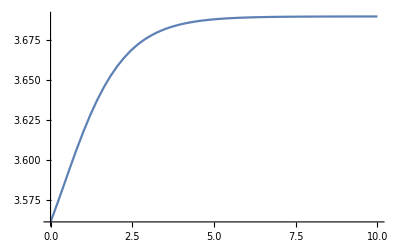

```mathematica
Plot[Z1[x,1,1],{x,0,10}, PlotRange->All]
```

```mathematica
Z2[x_,y_,z_]:=-(((x+z)^2-x^2)/(2y)+Log[(Cosh[y]+Cosh[x+z])/(Cosh[y]+Cosh[x])]+(PolyLog[2,-ⅇ^(y-(x+z))]+PolyLog[2,-ⅇ^(y+(x+z))]-PolyLog[2,-ⅇ^(y-x)]-PolyLog[2,-ⅇ^(y+x)])/y);
```

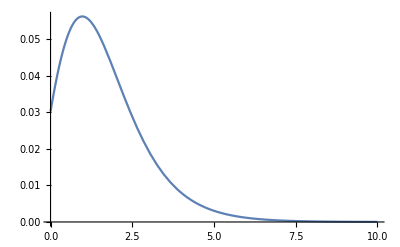

```mathematica
Plot[Z2[x,1,1],{x,0,10}, PlotRange->All]
```

```mathematica
SIMPY=Z1[ω,J,ω0]/(Exp[ω+ω0]+1)+Z1[ω,J,-ω0]/(Exp[ω-ω0]+1)+Z2[ω,J,ω0]/(Exp[ω0]-1)+Z2[ω,J,-ω0]/(Exp[-ω0]-1)
```

```mathematica
(-J+π^2/(6 J)-(ω-ω0)^2/(2 J)-Log[(Cosh[J]+Cosh[ω-ω0])/(-1+Cosh[J])]-(2 PolyLog[2,ⅇ^-J]+PolyLog[2,-ⅇ^(J+ω-ω0)]+PolyLog[2,-ⅇ^(J-ω+ω0)])/J)/(1+ⅇ^(ω-ω0))+1/(-1+ⅇ^-ω0)(-(-ω^2+(ω-ω0)^2)/(2 J)-Log[(Cosh[J]+Cosh[ω-ω0])/(Cosh[J]+Cosh[ω])]-(-PolyLog[2,-ⅇ^(J-ω)]-PolyLog[2,-ⅇ^(J+ω)]+PolyLog[2,-ⅇ^(J+ω-ω0)]+PolyLog[2,-ⅇ^(J-ω+ω0)])/J)+(-J+π^2/(6 J)-(ω+ω0)^2/(2 J)-Log[(Cosh[J]+Cosh[ω+ω0])/(-1+Cosh[J])]-(2 PolyLog[2,ⅇ^-J]+PolyLog[2,-ⅇ^(J-ω-ω0)]+PolyLog[2,-ⅇ^(J+ω+ω0)])/J)/(1+ⅇ^(ω+ω0))+1/(-1+ⅇ^ω0)(-(-ω^2+(ω+ω0)^2)/(2 J)-Log[(Cosh[J]+Cosh[ω+ω0])/(Cosh[J]+Cosh[ω])]-(-PolyLog[2,-ⅇ^(J-ω)]-PolyLog[2,-ⅇ^(J+ω)]+PolyLog[2,-ⅇ^(J-ω-ω0)]+PolyLog[2,-ⅇ^(J+ω+ω0)])/J)
```

```mathematica
Simplify[SIMPY-OG,Assumptions->ω>0&&J>0&&ω0>0];
```

```mathematica
Manipulate[N[%],{J,0.1,10},{ω0,-10,10},{ω,-10,10}]
```

```mathematica
Y[x_,y_]:=-y/2-Log[(ⅇ^(-x-y)+1)(ⅇ^(y-x)+1)]+(PolyLog[2,-ⅇ^(-y-x)]-PolyLog[2,-ⅇ^(y-x)]-2PolyLog[2,1-ⅇ^y])/y;
```

```mathematica
Tot=1/2 Z1[ω,J,ω0]/(Exp[ω+ω0]+1)+1/2 Z1[ω,J,-ω0]/(Exp[ω-ω0]+1)+1/2 Z2[ω,J,ω0]/(Exp[ω0]-1)+1/2 Z2[ω,J,-ω0]/(Exp[-ω0]-1)+Y[ω,J]/(Exp[ω0]-1);
```

```mathematica
Tot/.{ω->ω/T,J->π*J/T,ω0->ω0/T }
```

1/(2 (1+ⅇ^(ω/T-ω0/T)))(-(J π)/T+(π T)/(6 J)-(T (ω/T-ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π))+1/(2 (-1+ⅇ^(-ω0/T)))(-(T (-ω^2/T^2+(ω/T-ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-1/(J π)T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))+1/(2 (1+ⅇ^(ω/T+ω0/T)))(-(J π)/T+(π T)/(6 J)-(T (ω/T+ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))/(J π))+1/(2 (-1+ⅇ^(ω0/T)))(-(T (-ω^2/T^2+(ω/T+ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-1/(J π)T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))+(-(J π)/(2 T)-Log[(1+ⅇ^(-(J π)/T-ω/T)) (1+ⅇ^((J π)/T-ω/T))]+(T (PolyLog[2,-ⅇ^(-(J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-2 PolyLog[2,1-ⅇ^((J π)/T)]))/(J π))/(-1+ⅇ^(ω0/T))

```mathematica
Tauinv[ω_,ω0_,J_,T_]:=1/(2 (1+ⅇ^(ω/T-ω0/T)))(-(J π)/T+(π T)/(6 J)-(T (ω/T-ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π))+1/(2 (-1+ⅇ^(-ω0/T)))(-(T (-ω^2/T^2+(ω/T-ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-1/(J π)T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))+1/(2 (1+ⅇ^(ω/T+ω0/T)))(-(J π)/T+(π T)/(6 J)-(T (ω/T+ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))/(J π))+1/(2 (-1+ⅇ^(ω0/T)))(-(T (-ω^2/T^2+(ω/T+ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-1/(J π)T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))+(-(J π)/(2 T)-Log[(1+ⅇ^(-(J π)/T-ω/T)) (1+ⅇ^((J π)/T-ω/T))]+(T (PolyLog[2,-ⅇ^(-(J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-2 PolyLog[2,1-ⅇ^((J π)/T)]))/(J π))/(-1+ⅇ^(ω0/T));
```

```mathematica
Manipulate[Plot[Tauinv[0,ω0,1,T],{T,0.5,5}],{ω0,0.1,3}]
```

```mathematica
Manipulate[Plot[Tauinv[ω,ω0,1,T],{ω,0,10}, PlotRange->{0,5}],{T,0.3,5},{ω0,0.5,3}]
```

```mathematica
Manipulate[Plot[Tauinv[ω,ω0,1,T],{ω,0,10}, PlotRange->{0,5}],{T,1,5},{ω0,2,3}]
```

```mathematica
Manipulate[Plot[Tauinv[ω,ω0,1,T]/Tauinv[100,ω0,1,T],{ω,0,10}, PlotRange->{0,20}],{T,0.3,5},{ω0,0.1,3}]
```

```mathematica
Manipulate[Plot[Log[Tauinv[ω,ω0,10,T]],{ω,0,30}],{T,0.3,5},{ω0,0.1,3}]
```

```mathematica
N[Z2[0.1,0.001,3]]
```

1.3875×10^-7

```mathematica
Y[ω,J]/.{ω->ω/T,J->π*J/T}
```

-(J π)/(2 T)-Log[(1+ⅇ^(-(J π)/T-ω/T)) (1+ⅇ^((J π)/T-ω/T))]+(T (PolyLog[2,-ⅇ^(-(J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-2 PolyLog[2,1-ⅇ^((J π)/T)]))/(J π)

```mathematica
Tauinv2[ω_,ω0_,J_,T_]:=Tauinv[ω,ω0,J,T]+-(J π)/(2 T)-Log[(1+ⅇ^(-(J π)/T-ω/T)) (1+ⅇ^((J π)/T-ω/T))]+(T (PolyLog[2,-ⅇ^(-(J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-2 PolyLog[2,1-ⅇ^((J π)/T)]))/(J π)
```

```mathematica
Manipulate[Plot[Tauinv2[ω,ω0,1,T]/Tauinv2[10,ω0,1,T],{ω,0,10}, PlotRange->{0,2}],{T,0.3,5},{ω0,0.1,3}]
```

```mathematica
Limit[Z1[ω,J,ω0]/(Exp[ω+ω0]+1)+Z1[ω,J,-ω0]/(Exp[ω-ω0]+1)+Z2[ω,J,ω0]/(Exp[ω0]-1)+Z2[ω,J,-ω0]/(Exp[-ω0]-1),ω->∞]
```

Limit::zfun: Unable to determine whether expressions {2 ω ω0-ω0^2-2 ω Log[ⅇ^J]-Log[ⅇ^J]^2+2 ω Log[ⅇ^(J-ω0)]+Log[ⅇ^(J-ω0)]^2-2 J Log[ⅇ^-ω0],-2 ω ω0-ω0^2-2 ω Log[ⅇ^J]-Log[ⅇ^J]^2-2 J Log[ⅇ^ω0]+2 ω Log[ⅇ^(J+ω0)]+Log[ⅇ^(J+ω0)]^2} are equal to zero. Assuming they are.

ConditionalExpression[0, (ω0|J|PolyLog[2,ⅇ^-J])∈ℝ]

```mathematica
Limit[Z1[ω,J,ω0]/(Exp[ω+ω0]+1)+Z1[ω,J,-ω0]/(Exp[ω-ω0]+1)+Z2[ω,J,ω0]/(Exp[ω0]-1)+Z2[ω,J,-ω0]/(Exp[-ω0]-1),ω->0]
```

(-6 J^2+π^2-6 J Log[(Cosh[J]+Cosh[ω0])/(-1+Cosh[J])]+6 J Log[(Cosh[J]+Cosh[ω0])/(1+Cosh[J])]-12 PolyLog[2,ⅇ^-J]-12 PolyLog[2,-ⅇ^J])/(6 J)

```mathematica
(-6 J^2+π^2-6 J Log[(Cosh[J]+Cosh[ω0])/(-1+Cosh[J])]+6 J Log[(Cosh[J]+Cosh[ω0])/(1+Cosh[J])]-12 PolyLog[2,ⅇ^-J]-12 PolyLog[2,-ⅇ^J])/(6 J)/.{ω->ω/T,J->π*1/T,ω0->ω0/T }
```

(T (π^2-(6 π^2)/T^2-(6 π Log[(Cosh[π/T]+Cosh[ω0/T])/(-1+Cosh[π/T])])/T+(6 π Log[(Cosh[π/T]+Cosh[ω0/T])/(1+Cosh[π/T])])/T-12 PolyLog[2,ⅇ^(-π/T)]-12 PolyLog[2,-ⅇ^(π/T)]))/(6 π)

```mathematica
Manipulate[Plot[(T (π^2-(6 π^2)/T^2-(6 π Log[(Cosh[π/T]+Cosh[ω0/T])/(-1+Cosh[π/T])])/T+(6 π Log[(Cosh[π/T]+Cosh[ω0/T])/(1+Cosh[π/T])])/T-12 PolyLog[2,ⅇ^(-π/T)]-12 PolyLog[2,-ⅇ^(π/T)]))/(6 π),{T,0.5,5}],{ω0,0.1,3}]
```

```mathematica
Limit[Y[ω,J]/(Exp[ω0]-1),ω->0]
```

```mathematica
(-J/2-Log[(1+ⅇ^-J) (1+ⅇ^J)]+(PolyLog[2,-ⅇ^-J]-PolyLog[2,-ⅇ^J]-2 PolyLog[2,1-ⅇ^J])/J)/(-1+ⅇ^ω0)/.{ω->ω/T,J->π*1/T,ω0->ω0/T }
```

(-π/(2 T)-Log[(1+ⅇ^(-π/T)) (1+ⅇ^(π/T))]+(T (PolyLog[2,-ⅇ^(-π/T)]-PolyLog[2,-ⅇ^(π/T)]-2 PolyLog[2,1-ⅇ^(π/T)]))/π)/(-1+ⅇ^(ω0/T))

```mathematica
Manipulate[Plot[(-π/(2 T)-Log[(1+ⅇ^(-π/T)) (1+ⅇ^(π/T))]+(T (PolyLog[2,-ⅇ^(-π/T)]-PolyLog[2,-ⅇ^(π/T)]-2 PolyLog[2,1-ⅇ^(π/T)]))/π)/(-1+ⅇ^(ω0/T)),{T,0.5,5}],{ω0,0.1,3}]
```

```mathematica
Limit[Y[ω,J]/(Exp[ω0]-1),ω->∞]
```

(J^2+4 PolyLog[2,1-ⅇ^J])/(2 J-2 ⅇ^ω0 J)

```mathematica
(J^2+4 PolyLog[2,1-ⅇ^J])/(2 J-2 ⅇ^ω0 J)/.{ω->ω/T,J->π*1/T,ω0->ω0/T }
```

(π^2/T^2+4 PolyLog[2,1-ⅇ^(π/T)])/((2 π)/T-(2 ⅇ^(ω0/T) π)/T)

```mathematica
Manipulate[Plot[(π^2/T^2+4 PolyLog[2,1-ⅇ^(π/T)])/((2 π)/T-(2 ⅇ^(ω0/T) π)/T),{T,0.5,5}],{ω0,0.1,3}]
```

```mathematica
Manipulate[Plot[T^2(π^2/T^2+4 PolyLog[2,1-ⅇ^(π/T)])/((2 π)/T-(2 ⅇ^(ω0/T) π)/T)/((-π/(2 T)-Log[(1+ⅇ^(-π/T)) (1+ⅇ^(π/T))]+(T (PolyLog[2,-ⅇ^(-π/T)]-PolyLog[2,-ⅇ^(π/T)]-2 PolyLog[2,1-ⅇ^(π/T)]))/π)/(-1+ⅇ^(ω0/T))),{T,0.01,5}, PlotRange->All],{ω0,0.1,3}]
```

## Initial attempt at the saturating magnetoelastic

```mathematica
Totpre=1/2 Z1[ω,J,ω0]/(Exp[ω+ω0]+1)+1/2 Z1[ω,J,-ω0]/(Exp[ω-ω0]+1)+1/2 Z2[ω,J,ω0]/(Exp[ω0]-1)+1/2 Z2[ω,J,-ω0]/(Exp[-ω0]-1);
```

```mathematica
Totpre/.{ω->ω/T,J->π*J/T,ω0->ω0/T }
```

(-(J π)/T+(π T)/(6 J)-(T (ω/T-ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π))/(2 (1+ⅇ^(ω/T-ω0/T)))+(-(T (-ω^2/T^2+(ω/T-ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-(T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π))/(2 (-1+ⅇ^(-ω0/T)))+(-(J π)/T+(π T)/(6 J)-(T (ω/T+ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))/(J π))/(2 (1+ⅇ^(ω/T+ω0/T)))+(-(T (-ω^2/T^2+(ω/T+ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-(T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))/(J π))/(2 (-1+ⅇ^(ω0/T)))

```mathematica
taupre[ω_,ω0_,J_,T_]:=(-(J π)/T+(π T)/(6 J)-(T (ω/T-ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π))/(2 (1+ⅇ^(ω/T-ω0/T)))+(-(T (-ω^2/T^2+(ω/T-ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-(T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π))/(2 (-1+ⅇ^(-ω0/T)))+(-(J π)/T+(π T)/(6 J)-(T (ω/T+ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))/(J π))/(2 (1+ⅇ^(ω/T+ω0/T)))+(-(T (-ω^2/T^2+(ω/T+ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-(T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))/(J π))/(2 (-1+ⅇ^(ω0/T)))
```

```mathematica
Manipulate[Plot[{taupre[ω,ω0,1,T],(π T)/(6 J+6 ⅇ^(ω/T) J)-(J π)/(T+ⅇ^(ω/T) T)-ω/(J π)-ω^2/(2 J π T+2 ⅇ^(ω/T) J π T)+1/(1+ⅇ^((2 ω)/T)+2 ⅇ^(ω/T) Cosh[(J π)/T])-ⅇ^((2 ω)/T)/(1+ⅇ^((2 ω)/T)+2 ⅇ^(ω/T) Cosh[(J π)/T])-(T Log[1+ⅇ^((J π-ω)/T)])/((1+ⅇ^(ω/T)) J π)-(ⅇ^(ω/T) T Log[1+ⅇ^((J π-ω)/T)])/((1+ⅇ^(ω/T)) J π)+(T Log[1+ⅇ^((J π+ω)/T)])/((1+ⅇ^(ω/T)) J π)+(ⅇ^(ω/T) T Log[1+ⅇ^((J π+ω)/T)])/((1+ⅇ^(ω/T)) J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T])/(-1+Cosh[(J π)/T])]/(1+ⅇ^(ω/T))-(2 T PolyLog[2,ⅇ^(-(J π)/T)])/(J π+ⅇ^(ω/T) J π)-(T PolyLog[2,-ⅇ^((J π+ω)/T)])/((1+ⅇ^(ω/T)) J π)-(T PolyLog[2,-ⅇ^((J π)/T-ω/T)])/(J π+ⅇ^(ω/T) J π)/.J->1},{ω,0,20}, PlotRange->All],{T,0.3,5},{ω0,0.000001,100}]
```

```mathematica
Limit[taupre[ω,ω0,J,T],ω0->0]
```

(π T)/(6 J+6 ⅇ^(ω/T) J)-(J π)/(T+ⅇ^(ω/T) T)-ω/(J π)-ω^2/(2 J π T+2 ⅇ^(ω/T) J π T)+1/(1+ⅇ^((2 ω)/T)+2 ⅇ^(ω/T) Cosh[(J π)/T])-ⅇ^((2 ω)/T)/(1+ⅇ^((2 ω)/T)+2 ⅇ^(ω/T) Cosh[(J π)/T])-(T Log[1+ⅇ^((J π-ω)/T)])/((1+ⅇ^(ω/T)) J π)-(ⅇ^(ω/T) T Log[1+ⅇ^((J π-ω)/T)])/((1+ⅇ^(ω/T)) J π)+(T Log[1+ⅇ^((J π+ω)/T)])/((1+ⅇ^(ω/T)) J π)+(ⅇ^(ω/T) T Log[1+ⅇ^((J π+ω)/T)])/((1+ⅇ^(ω/T)) J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T])/(-1+Cosh[(J π)/T])]/(1+ⅇ^(ω/T))-(2 T PolyLog[2,ⅇ^(-(J π)/T)])/(J π+ⅇ^(ω/T) J π)-(T PolyLog[2,-ⅇ^((J π+ω)/T)])/((1+ⅇ^(ω/T)) J π)-(T PolyLog[2,-ⅇ^((J π)/T-ω/T)])/(J π+ⅇ^(ω/T) J π)

```mathematica
Totpre2=+Y[ω,J]/(Exp[ω0]-1);
```

```mathematica
Totpre2/.{ω->ω/T,J->π*J/T,ω0->ω0/T }
```

(-(J π)/(2 T)-Log[(1+ⅇ^(-(J π)/T-ω/T)) (1+ⅇ^((J π)/T-ω/T))]+(T (PolyLog[2,-ⅇ^(-(J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-2 PolyLog[2,1-ⅇ^((J π)/T)]))/(J π))/(-1+ⅇ^(ω0/T))

```mathematica
taupre2[ω_,ω0_,J_,T_]:=(-(J π)/(2 T)-Log[(1+ⅇ^(-(J π)/T-ω/T)) (1+ⅇ^((J π)/T-ω/T))]+(T (PolyLog[2,-ⅇ^(-(J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-2 PolyLog[2,1-ⅇ^((J π)/T)]))/(J π))/(-1+ⅇ^(ω0/T))
```

```mathematica
Manipulate[Plot[taupre2[ω,ω0,1,T],{ω,0,100}, PlotRange->{0,20}],{T,0.3,5},{ω0,0.1,30}]
```

```mathematica
tauprePhon[ω_,ω0_,T_]:=2 1/(Exp[ω0/T]-1)+1/(Exp[(ω0+ω)/T]+1)+1/(Exp[(ω0-ω)/T]+1)
```

```mathematica
Manipulate[Plot[tauprePhon[ω,ω0,T],{ω,-100,100}, PlotRange->{0,20}],{T,0.3,10},{ω0,0.1,30}]
```

```mathematica
Manipulate[Plot[1/(Exp[(ω0+ω)/T]+1)+1/(Exp[(ω-ω0)/T]+1),{ω,0,100}, PlotRange->{0,20}],{T,0.3,10},{ω0,0.1,30}]
```

# After the correction

```mathematica
Y[x_,y_]:=-y/2-Log[(ⅇ^(-x-y)+1)(ⅇ^(y-x)+1)]+(PolyLog[2,-ⅇ^(-y-x)]-PolyLog[2,-ⅇ^(y-x)]-2PolyLog[2,1-ⅇ^y])/y;
```

```mathematica
Z1[x_,y_,z_]:=-(y+(x+z)^2/(2y)-π^2/(6y)+(PolyLog[2,-ⅇ^(y-(x+z))]+PolyLog[2,-ⅇ^(y+(x+z))]+2PolyLog[2,ⅇ^-y])/y+Log[(Cosh[y]+Cosh[x+z])/(Cosh[y]-1)]);
```

```mathematica
Z2[x_,y_,z_]:=-(((x+z)^2-x^2)/(2y)+Log[(Cosh[y]+Cosh[x+z])/(Cosh[y]+Cosh[x])]+(PolyLog[2,-ⅇ^(y-(x+z))]+PolyLog[2,-ⅇ^(y+(x+z))]-PolyLog[2,-ⅇ^(y-x)]-PolyLog[2,-ⅇ^(y+x)])/y);
```

```mathematica
Tot=1/2 Z1[ω,J,ω0]/(Exp[ω+ω0]+1)+1/2 Z1[-ω,J,ω0]/(Exp[ω0-ω]+1)+1/2 Z2[ω,J,ω0]/(Exp[ω0]-1)+1/2 Z2[-ω,J,ω0]/(Exp[ω0-2ω]-1)+Y[ω,J]/(Exp[ω0]-1);
```

```mathematica
Tot/.{ω->ω/T,J->π*J/T,ω0->ω0/T }
```

(-(J π)/T+(π T)/(6 J)-(T (-ω/T+ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π))/(2 (1+ⅇ^(-ω/T+ω0/T)))+(-(T (-ω^2/T^2+(-ω/T+ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-(T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π))/(2 (-1+ⅇ^(-(2 ω)/T+ω0/T)))+(-(J π)/T+(π T)/(6 J)-(T (ω/T+ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))/(J π))/(2 (1+ⅇ^(ω/T+ω0/T)))+(-(T (-ω^2/T^2+(ω/T+ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-(T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))/(J π))/(2 (-1+ⅇ^(ω0/T)))+(-(J π)/(2 T)-Log[(1+ⅇ^(-(J π)/T-ω/T)) (1+ⅇ^((J π)/T-ω/T))]+(T (PolyLog[2,-ⅇ^(-(J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-2 PolyLog[2,1-ⅇ^((J π)/T)]))/(J π))/(-1+ⅇ^(ω0/T))

```mathematica
Tauinv[ω_,ω0_,J_,T_]:=(-(J π)/T+(π T)/(6 J)-(T (-ω/T+ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π))/(2 (1+ⅇ^(-ω/T+ω0/T)))+(-(T (-ω^2/T^2+(-ω/T+ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-(T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π))/(2 (-1+ⅇ^(-(2 ω)/T+ω0/T)))+(-(J π)/T+(π T)/(6 J)-(T (ω/T+ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))/(J π))/(2 (1+ⅇ^(ω/T+ω0/T)))+(-(T (-ω^2/T^2+(ω/T+ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-(T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))/(J π))/(2 (-1+ⅇ^(ω0/T)))+(-(J π)/(2 T)-Log[(1+ⅇ^(-(J π)/T-ω/T)) (1+ⅇ^((J π)/T-ω/T))]+(T (PolyLog[2,-ⅇ^(-(J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-2 PolyLog[2,1-ⅇ^((J π)/T)]))/(J π))/(-1+ⅇ^(ω0/T))
```

```mathematica
Manipulate[Plot[{2*π*Tauinv[0,ω0,1,T],Tauinv[0,ω0,0.0001,T]},{T,0.1,5}],{ω0,0.1,3}]
```

```mathematica
Manipulate[Plot[{Tauinv[0,ω0,1,T],Tauinv[0,ω0,0.0001,T]},{T,0.1,5}],{ω0,0.1,3}]
```

```mathematica
Manipulate[Plot[Tauinv[ω,ω0,1,T],{ω,0,10}, PlotRange->{0,5}],{T,0.3,5},{ω0,0.5,3}]
```

```mathematica
Tot2=1/2 2/(Exp[ω+ω0]+1)+1/2 2/(Exp[ω0-ω]+1)+2/(Exp[ω0]-1);
```

```mathematica
Tot2/.{ω->ω/T,J->π*J/T,ω0->ω0/T }
```

2/(-1+ⅇ^(ω0/T))+1/(1+ⅇ^(-ω/T+ω0/T))+1/(1+ⅇ^(ω/T+ω0/T))

## Additional checks, there might have been a mistake above

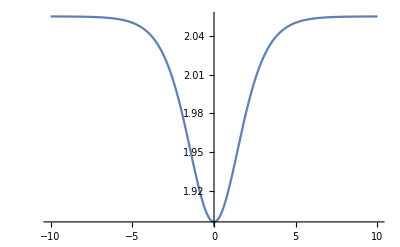

```mathematica
Plot[Y[ω,1],{ω,-10,10}]
```

```mathematica
Tot=1/2 Z1[ω,J,ω0]/(Exp[ω+ω0]+1)-1/2 Z1[ω,J,-ω0]/(Exp[ω-ω0]+1)+1/2 Z2[ω,J,ω0]/(Exp[ω0]-1)-1/2 Z2[ω,J,-ω0]/(Exp[ω0]-1)+Y[ω,J](1/(Exp[ω0]-1)+1/2);
```

```mathematica
Tot/.{ω->ω/T,J->π*J/T,ω0->ω0/T }
```

-(-(J π)/T+(π T)/(6 J)-(T (ω/T-ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π))/(2 (1+ⅇ^(ω/T-ω0/T)))-(-(T (-ω^2/T^2+(ω/T-ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-(T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π))/(2 (-1+ⅇ^(ω0/T)))+(-(J π)/T+(π T)/(6 J)-(T (ω/T+ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))/(J π))/(2 (1+ⅇ^(ω/T+ω0/T)))+(-(T (-ω^2/T^2+(ω/T+ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-(T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))/(J π))/(2 (-1+ⅇ^(ω0/T)))+(1/2+1/(-1+ⅇ^(ω0/T))) (-(J π)/(2 T)-Log[(1+ⅇ^(-(J π)/T-ω/T)) (1+ⅇ^((J π)/T-ω/T))]+(T (PolyLog[2,-ⅇ^(-(J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-2 PolyLog[2,1-ⅇ^((J π)/T)]))/(J π))

```mathematica
Tauinv[ω_,ω0_,J_,T_]:=-(-(J π)/T+(π T)/(6 J)-(T (ω/T-ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π))/(2 (1+ⅇ^(ω/T-ω0/T)))-(-(T (-ω^2/T^2+(ω/T-ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-(T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π))/(2 (-1+ⅇ^(ω0/T)))+(-(J π)/T+(π T)/(6 J)-(T (ω/T+ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))/(J π))/(2 (1+ⅇ^(ω/T+ω0/T)))+(-(T (-ω^2/T^2+(ω/T+ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-(T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))/(J π))/(2 (-1+ⅇ^(ω0/T)))+(1/2+1/(-1+ⅇ^(ω0/T))) (-(J π)/(2 T)-Log[(1+ⅇ^(-(J π)/T-ω/T)) (1+ⅇ^((J π)/T-ω/T))]+(T (PolyLog[2,-ⅇ^(-(J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-2 PolyLog[2,1-ⅇ^((J π)/T)]))/(J π))
```

```mathematica
Manipulate[Plot[{Tauinv[0,ω0,1,T],Tauinv[0,ω0,0.0001,T]},{T,0.1,5}],{ω0,0.1,3}]
```

```mathematica
Manipulate[Plot[Tauinv[ω,ω0,1,T],{ω,0,10}, PlotRange->{-5,5}],{T,0.3,5},{ω0,0.5,30}]
```

```mathematica
Manipulate[Plot[2/(-1+ⅇ^(ω0/T))+1/(1+ⅇ^(-ω/T+ω0/T))+1/(1+ⅇ^(ω/T+ω0/T)),{ω,0,10}, PlotRange->{0,5}],{T,0.03,5},{ω0,0.5,3}]
```

```mathematica
Tot2=1/2 Z1[ω,J,ω0]/(Exp[ω+ω0]+1)+1/2 Z1[ω,J,-ω0]/(Exp[ω0-ω]+1)+1/2 Z2[ω,J,ω0]/(Exp[ω0]-1)+1/2 Z2[ω,J,-ω0]/(Exp[ω0]-1)+Y[ω,J]/(Exp[ω0]-1)+(Y[ω,J]-Z1[ω,J,-ω0]+Z2[ω,J,-ω0])/2;
```

```mathematica
Tot2=1/2 Z1[ω,J,ω0]/(Exp[ω+ω0]+1)-1/2 Z1[ω,J,-ω0]/(Exp[ω-ω0]+1)+1/2 Z2[ω,J,ω0]/(Exp[ω0]-1)-1/2 Z2[ω,J,-ω0]/(Exp[-ω0]-1)+Y[ω,J](1/(Exp[ω0]-1)+1/2);
```

```mathematica
Tot2=1/2 Z1[ω,J,ω0]/(Exp[ω+ω0]+1)-1/2 Z1[ω,J,-ω0]/(Exp[ω-ω0]+1)+1/2 Z2[ω,J,ω0]/(Exp[ω0]-1)-1/2 Z2[ω,J,-ω0]/(Exp[-ω0]-1)+Y[ω,J](1/(Exp[ω0]-1)+1/2);
```

```mathematica
Tot2/.{ω->ω/T,J->π*J/T,ω0->ω0/T }
```

(-(J π)/T+(π T)/(6 J)-(T (ω/T-ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π))/(2 (1+ⅇ^(-ω/T+ω0/T)))+(-(T (-ω^2/T^2+(ω/T-ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-(T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π))/(2 (-1+ⅇ^(ω0/T)))+(-(J π)/T+(π T)/(6 J)-(T (ω/T+ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))/(J π))/(2 (1+ⅇ^(ω/T+ω0/T)))+(-(T (-ω^2/T^2+(ω/T+ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-(T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))/(J π))/(2 (-1+ⅇ^(ω0/T)))+(-(J π)/(2 T)-Log[(1+ⅇ^(-(J π)/T-ω/T)) (1+ⅇ^((J π)/T-ω/T))]+(T (PolyLog[2,-ⅇ^(-(J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-2 PolyLog[2,1-ⅇ^((J π)/T)]))/(J π))/(-1+ⅇ^(ω0/T))+1/2 ((J π)/(2 T)-(π T)/(6 J)+(T (ω/T-ω0/T)^2)/(2 J π)-(T (-ω^2/T^2+(ω/T-ω0/T)^2))/(2 J π)-Log[(1+ⅇ^(-(J π)/T-ω/T)) (1+ⅇ^((J π)/T-ω/T))]+Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(-1+Cosh[(J π)/T])]-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]+(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π)-(T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π)+(T (PolyLog[2,-ⅇ^(-(J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-2 PolyLog[2,1-ⅇ^((J π)/T)]))/(J π))

```mathematica
Tauinv1[ω_,ω0_,J_,T_]:=(-(J π)/T+(π T)/(6 J)-(T (ω/T-ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π))/(2 (1+ⅇ^(-ω/T+ω0/T)))+(-(T (-ω^2/T^2+(ω/T-ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-(T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π))/(2 (-1+ⅇ^(ω0/T)))+(-(J π)/T+(π T)/(6 J)-(T (ω/T+ω0/T)^2)/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))/(J π))/(2 (1+ⅇ^(ω/T+ω0/T)))+(-(T (-ω^2/T^2+(ω/T+ω0/T)^2))/(2 J π)-Log[(Cosh[(J π)/T]+Cosh[ω/T+ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]-(T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T+ω0/T)]))/(J π))/(2 (-1+ⅇ^(ω0/T)))+(-(J π)/(2 T)-Log[(1+ⅇ^(-(J π)/T-ω/T)) (1+ⅇ^((J π)/T-ω/T))]+(T (PolyLog[2,-ⅇ^(-(J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-2 PolyLog[2,1-ⅇ^((J π)/T)]))/(J π))/(-1+ⅇ^(ω0/T))+1/2 ((J π)/(2 T)-(π T)/(6 J)+(T (ω/T-ω0/T)^2)/(2 J π)-(T (-ω^2/T^2+(ω/T-ω0/T)^2))/(2 J π)-Log[(1+ⅇ^(-(J π)/T-ω/T)) (1+ⅇ^((J π)/T-ω/T))]+Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(-1+Cosh[(J π)/T])]-Log[(Cosh[(J π)/T]+Cosh[ω/T-ω0/T])/(Cosh[(J π)/T]+Cosh[ω/T])]+(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π)-(T (-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T+ω/T)]+PolyLog[2,-ⅇ^((J π)/T+ω/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T-ω/T+ω0/T)]))/(J π)+(T (PolyLog[2,-ⅇ^(-(J π)/T-ω/T)]-PolyLog[2,-ⅇ^((J π)/T-ω/T)]-2 PolyLog[2,1-ⅇ^((J π)/T)]))/(J π))
```

```mathematica
Manipulate[Plot[{Tauinv1[0,ω0,1,T],Tauinv[0,ω0,1,T],2/(-1+ⅇ^(ω0/T))+1/(1+ⅇ^(+ω0/T))+1/(1+ⅇ^(ω0/T))},{T,0.1,5}],{ω0,0.1,3}]
```

## Dc calc

```mathematica
Totprime=((2/(Exp[ω0]+1)-1)Z1[0,J,ω0]+(2/(Exp[ω0]-1)+1)(Y[0,J]+Z2[0,J,ω0]))/2;
```

```mathematica
Totprime/.{ω->ω/T,J->π*J/T,ω0->ω0/T }
```

1/2 ((-1+2/(1+ⅇ^(ω0/T))) (-(J π)/T+(π T)/(6 J)-ω0^2/(2 J π T)-Log[(Cosh[(J π)/T]+Cosh[ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω0/T)]))/(J π))+(1+2/(-1+ⅇ^(ω0/T))) (-(J π)/(2 T)-ω0^2/(2 J π T)-Log[(1+ⅇ^(-(J π)/T)) (1+ⅇ^((J π)/T))]-Log[(Cosh[(J π)/T]+Cosh[ω0/T])/(1+Cosh[(J π)/T])]-(T (-2 PolyLog[2,-ⅇ^((J π)/T)]+PolyLog[2,-ⅇ^((J π)/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω0/T)]))/(J π)+(T (PolyLog[2,-ⅇ^(-(J π)/T)]-PolyLog[2,-ⅇ^((J π)/T)]-2 PolyLog[2,1-ⅇ^((J π)/T)]))/(J π)))

```mathematica
Tauinv2[ω_,ω0_,J_,T_]:=1/2 ((-1+2/(1+ⅇ^(ω0/T))) (-(J π)/T+(π T)/(6 J)-ω0^2/(2 J π T)-Log[(Cosh[(J π)/T]+Cosh[ω0/T])/(-1+Cosh[(J π)/T])]-(T (2 PolyLog[2,ⅇ^(-(J π)/T)]+PolyLog[2,-ⅇ^((J π)/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω0/T)]))/(J π))+(1+2/(-1+ⅇ^(ω0/T))) (-(J π)/(2 T)-ω0^2/(2 J π T)-Log[(1+ⅇ^(-(J π)/T)) (1+ⅇ^((J π)/T))]-Log[(Cosh[(J π)/T]+Cosh[ω0/T])/(1+Cosh[(J π)/T])]-(T (-2 PolyLog[2,-ⅇ^((J π)/T)]+PolyLog[2,-ⅇ^((J π)/T-ω0/T)]+PolyLog[2,-ⅇ^((J π)/T+ω0/T)]))/(J π)+(T (PolyLog[2,-ⅇ^(-(J π)/T)]-PolyLog[2,-ⅇ^((J π)/T)]-2 PolyLog[2,1-ⅇ^((J π)/T)]))/(J π)))
```

```mathematica
Manipulate[Plot[{Tauinv2[0,ω0,1,T],Tauinv1[0,ω0,1,T],Tauinv[0,ω0,1,T],2/(-1+ⅇ^(ω0/T))+1/(1+ⅇ^(+ω0/T))+1/(1+ⅇ^(ω0/T))},{T,0.1,5}],{ω0,0.1,3}]
```